## Datos v2 Phoenix 20-40%

```mathematica
v2P2040={{0.50,0.0964,0.0125,-0.00113,0.0133,-0.0113},{0.70,0.0668,0.0173,-0.0289,0.0336,-0.0485},{0.90,0.0640,0.0178,-0.0281,0.0308,-0.0555},{1.10,0.0866,0.0155,-0.0217,0.0240,-0.0403},{1.30,0.1251,0.0146,-0.0170,0.0178,-0.0240},{1.50,0.1405,0.0182,-0.0202,0.0185,-0.0227},{1.70,0.2074,0.0316,-0.0269,0.0291,-0.0212},{1.90,0.1511,0.0314,-0.0342,0.0207,-0.0245},{2.25,0.1846,0.0279,-0.0273,0.0186,-0.0174},{3.0,0.1412,0.0407,-0.0431,0.0137,-0.0160},{4.25,0.1561,0.1048,-0.0992,0.0133,-0.0121}};
```

```mathematica
v2P2040c={{1.19,0.0902,0.0097,-0.0151,0.0236,-0.0377},{1.69,0.1403,0.0066,-0.0104,0.0185,-0.0248},{2.20,0.1649,0.0046,-0.0056,0.0188,-0.0202},{2.70,0.1592,0.0071,-0.0083,0.0189,-0.0200},{3.20,0.1327,0.0098,-0.0136,0.0190,-0.0216},{3.85,0.0972,0.0155,-0.0277,0.0153,-0.0192}};
```

### Datos con barras de error:

```mathematica
Needs["ErrorBarPlots`"]
```

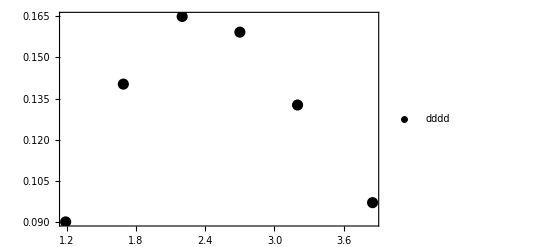

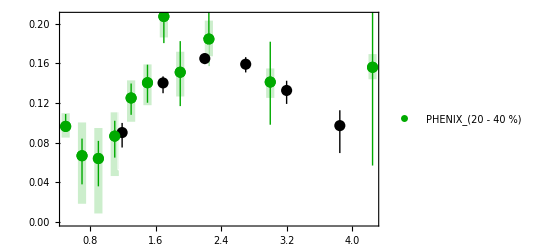

```mathematica
v2P20401=ErrorListPlot[Table[{{v2P2040[[i,1]],v2P2040[[i,2]]},ErrorBar[0.05,{v2P2040[[i,5]],v2P2040[[i,6]]}]},{i,1,Length[v2P2040]}],Frame->True,PlotStyle->{Darker[Green]},PlotRange-> Full,ErrorBarFunction->Function[{coords, errs}, {Opacity[0.2],Rectangle[coords+{errs⟦1,1⟧,errs⟦2,1⟧},coords+{errs⟦1,2⟧,errs⟦2,2⟧}]}]];
v2P20402=ErrorListPlot[Table[{{v2P2040[[i,1]],v2P2040[[i,2]]},ErrorBar[{0,0},{v2P2040[[i,3]],v2P2040[[i,4]]}]},{i,1,Length[v2P2040]}],Frame->True,PlotStyle->{Darker[Green],Thick,PointSize[.02]},PlotRange-> Full];
v2P2040c1=ErrorListPlot[Table[{{v2P2040c[[i,1]],v2P2040c[[i,2]]},ErrorBar[0.05,{v2P2040c[[i,5]],v2P2040c[[i,6]]}]},{i,1,Length[v2P2040c]}],Frame->True,PlotStyle->{EdgeForm[Thick],White},PlotRange-> Full,ErrorBarFunction->Function[{coords, errs}, {Opacity[0.2],Rectangle[coords+{errs⟦1,1⟧,errs⟦2,1⟧},coords+{errs⟦1,2⟧,errs⟦2,2⟧}]}]];
v2P2040c2=ErrorListPlot[Table[{{v2P2040c[[i,1]],v2P2040c[[i,2]]},ErrorBar[{0,0},{v2P2040c[[i,3]],v2P2040c[[i,4]]}]},{i,1,Length[v2P2040c]}],Frame->True,PlotStyle->{Black,Thick,PointSize[.02]},PlotRange-> Full];
Dat=ListPlot[Table[{v2P2040[[i,1]],v2P2040[[i,2]]},{i,1,Length[v2P2040]}],PlotStyle->{Darker[Green],Thick,PointSize[.02]},Frame->True,PlotRange->Full,PlotLegends->Placed[PointLegend[{Style["PHENIX_(20 - 40  %)",24]},LegendMarkers-> {Graphics[{Darker[Green],Rectangle[{0,0},{.05,1}],Disk[{0.025,.5},.3],Black,Rectangle[{0.8,0},{.85,1}],Disk[{0.825,.5},.3]}]},LegendMarkerSize->24],{Left,Top}]];
Datc=ListPlot[Table[{v2P2040c[[i,1]],v2P2040c[[i,2]]},{i,1,Length[v2P2040c]}],PlotStyle->{Black,Thick,PointSize[.02]},Frame->True,PlotRange->Full,PlotLegends->Placed[PointLegend[{Style["dddd",20]},LegendMarkers-> {Graphics[{Darker[Green],Rectangle[{0,0.5},{.05,1.5}],Disk[{0.025,1},.3]}]},LegendMarkerSize->20],{Right,Center}]]
Show[v2P20401,v2P20402,v2P2040c1,v2P2040c2,Dat]
```

## Modelo Hidrodinámico v2

```mathematica
HYDRO2040thermal=Interpolation[{{0.2000000000000000111`18.301029995663985,0.0305005500643512998700000000000000000000013296612030438073`18.484307671732306},{0.4000000000000000222`18.602059991327966,0.0427924608912324255800000000000000000000073491781352208381`18.63136726243045},{0.5999999999999999778`18.778151250383644,0.0580685150590251400500000000000000000000005955632477208946`18.763940720300294},{0.8000000000000000444`18.903089986991944,0.0775816385048631318400000000000000000000003430309055677914`18.889758947552078},{1.`18.,0.0973139335962632662200000000000000000000134711631381218014`18.98817502784011},{1.199999999999999956`18.079181246047625,0.11441310766831575`18.058475781991305},{1.399999999999999911`18.146128035678238,0.1275053042608729204`18.1055282519332},{1.600000000000000089`18.204119982655925,0.1361318552841612461`18.13395976337628},{1.800000000000000044`18.255272505103306,0.1403425266309571706`18.14718929100429},{2.`18.301029995663985,0.1404729978956515413`18.14759285098892},{2.200000000000000178`18.342422680822207,0.1370183202170487669`18.136778638961076},{2.399999999999999911`18.380211241711606,0.1305471056782632477`18.115767247649632},{2.600000000000000089`18.414973347970818,0.1216383652566975365`18.085070574865995},{2.799999999999999822`18.44715803134222,0.1108323881741993394`18.044666691348215},{3.`18.477121254719663,0.0985965076490250419399999999999999999999900573144009705661`18.99386153222703}}]
```

InterpolatingFunction[{{0.200000000000000011, 3.00000000000000000}}, <>]

```mathematica
HYDRO2040=Interpolation[{{2.000000000000000111*10^-01,1.408774854310947816*10^-02},{4.000000000000000222*10^-01,2.196804389459026952*10^-02},{5.999999999999999778*10^-01,3.744133932432755496*10^-02},{8.000000000000000444*10^-01,5.344803650875060153*10^-02},{1.000000000000000000*10^+00,6.808848931988641107*10^-02},{1.199999999999999956*10^+00,7.804864507108777438*10^-02},{1.399999999999999911*10^+00,8.343041897426850539*10^-02},{1.600000000000000089*10^+00,8.387284230525282602*10^-02},{1.800000000000000044*10^+00,8.035784082733626876*10^-02},{2.000000000000000000*10^+00,7.361366710730166130*10^-02},{2.200000000000000178*10^+00,6.481238573243014445*10^-02},{2.399999999999999911*10^+00,5.490725719001884192*10^-02},{2.600000000000000089*10^+00,4.476279877812262137*10^-02},{2.799999999999999822*10^+00,3.523643344619695889*10^-02},{3.000000000000000000*10^+00,2.681173560915485823*10^-02}}]
```

InterpolatingFunction[{{0.200000000000000011, 3.00000000000000000}}, <>]

## Datos yield Phoenix 20-40%

```mathematica
yP2040={{0.50,5.9544,1.5905,2.1162},{0.70,0.90647,0.3509,0.5883},{0.90,0.396036,0.1219,0.2095},{1.10,0.215631,0.0509,0.08410},{1.30,0.11057,0.02321,0.03606},{1.50,0.050032,0.01101,0.01594},{1.70,0.019825,0.0055,0.0072},{1.90,0.011294,0.0030,0.0035},{2.25,0.004157,0.00092,0.00114},{3,0.000554,0.00014,0.00014},{4.25,0.00004,0.000018,0.000009}};
```

## Modelo Hidrodinámico yield

```mathematica
yPG={{0.2000000000000000111`18.301029995663985,53.44945136229311088999999999999999999999`18.727943251704733},{0.4000000000000000222`18.602059991327966,4.772775589845908328`18.678771014843345},{0.5999999999999999778`18.778151250383644,1.071585904268862244`18.03002699222759},{0.8000000000000000444`18.903089986991944,0.3345673166134718879`18.52448351311262},{1.`18.,0.1232024314583608643`18.090619278920364},{1.199999999999999956`18.079181246047625,0.0505234752747985363399999999999999999999884786088568285705`18.70349321600757},{1.399999999999999911`18.146128035678238,0.0223831870504245036800000000000000000000089872436164768631`18.349921924009525},{1.600000000000000089`18.204119982655925,0.0105885135567412094799999999999999999999957813005627607506`18.024834996989913},{1.800000000000000044`18.255272505103306,0.0052987977727813571900000000000000000000008310672573866773`18.724177345096315},{2.`18.301029995663985,0.0027916104710789726300000000000000000000011283658874183188`18.445854818656343},{2.200000000000000178`18.342422680822207,0.0015413396702855922979999999999999999999989190705460373565`18.187898356223354},{2.399999999999999911`18.380211241711606,0.0008887360520633618646999999999999999999999590821935263633`18.94877279791847},{2.600000000000000089`18.414973347970818,0.0005334954091426797381000000000000000000000816747156309679`18.727130686567275},{2.799999999999999822`18.44715803134222,0.0003324049362030169766999999999999999999999615594511058981`18.52166746441958},{3.`18.477121254719663,0.0002143025333574363777000000000000000000000847900037277591`18.33102730504394},{3.200000000000000178`18.505149978319906,0.0001424290026209369024999999999999999999998863290160943248`18.15359843309105},{3.399999999999999911`18.531478917042257,0.000097422215425858876970000000000000000000001994014584097`18.988658001403742},{3.600000000000000089`18.556302500767288,0.0000683001222496351314700000000000000000000126537459276587`18.83442148102113},{3.799999999999999822`18.57978359661681,0.00004894994871483157019999999999999999999998923175017482`18.689752241126342},{4.`18.602059991327966,0.0000357772188803497578399999999999999999999893656367438088`18.55360657793451}};
yth={{0.2000000000000000111`18.301029995663985,10.03750670326943427999999999999999999998`18.001625848318316},{0.4000000000000000222`18.602059991327966,1.742585687465231459`18.24119414268302},{0.5999999999999999778`18.778151250383644,0.5062816469880110359`18.704392184237918},{0.8000000000000000444`18.903089986991944,0.1787840720005868245`18.252328824580797},{1.`18.,0.0699558159836027732`18.84482382668468},{1.199999999999999956`18.079181246047625,0.02925572479418580424`18.466210861982415},{1.399999999999999911`18.146128035678238,0.01285484121406479073`18.10906671650736},{1.600000000000000089`18.204119982655925,0.005879594444600773004`18.76934737088119},{1.800000000000000044`18.255272505103306,0.002783309832832603532`18.444561553872607},{2.`18.301029995663985,0.001358242070972440121`18.132977178426565},{2.200000000000000178`18.342422680822207,0.0006811586802374373006`18.833248295354654},{2.399999999999999911`18.380211241711606,0.0003501340786509636637`18.544234382829554},{2.600000000000000089`18.414973347970818,0.0001840416378458802483`18.26491608953659},{2.799999999999999822`18.44715803134222,0.00009870922680294322684`18.994357750058846},{3.`18.477121254719663,0.00005391343678350045805`18.731697017388562}};
ync={{0.2000000000000000111`18.301029995663985,4.305830715629349825`18.63405695147139},{0.4000000000000000222`18.602059991327966,0.4758412793422950871`18.677462114483404},{0.5999999999999999778`18.778151250383644,0.1163372250726599777`18.06571870060036},{0.8000000000000000444`18.903089986991944,0.03310303760142826318`18.519867847340972},{1.`18.,0.0100056678789736276`18.000246083124352},{1.199999999999999956`18.079181246047625,0.003254495387742644026`18.512483660398},{1.399999999999999911`18.146128035678238,0.001078625096137154167`18.03287052070561},{1.600000000000000089`18.204119982655925,0.0003765280570342332362`18.57579734324894},{1.800000000000000044`18.255272505103306,0.0001347333673791710018`18.129475164201715},{2.`18.301029995663985,0.00005025529746799580497`18.701181847980223},{2.200000000000000178`18.342422680822207,0.00001909357916831495592`18.280887346274724},{2.399999999999999911`18.380211241711606,7.193142264277305672`18.85691864975993*^-6},{2.600000000000000089`18.414973347970818,2.614004783195540911`18.41730637793218*^-6},{2.799999999999999822`18.44715803134222,8.971021129522794291`18.952841879574414*^-7},{3.`18.477121254719663,2.818864631060251513`18.450074220463602*^-7}};
```

```mathematica
yth[[1]][[2]]
```

10.0375067032694343

```mathematica
ynpm=Evaluate[Table[{yth[[i]][[1]],yth[[i]][[2]]+ync[[i]][[2]]},{i,1,15}]]
```

{{0.200000000000000011,14.3433374188987841},{0.400000000000000022,2.21842696680752655},{0.599999999999999978,0.622618872060671014},{0.800000000000000044,0.211887109602015088},{1.,0.0799614838625764008},{1.19999999999999996,0.0325102201819284483},{1.39999999999999991,0.0139334663102019449},{1.60000000000000009,0.00625612250163500624},{1.80000000000000004,0.00291804320021177453},{2.,0.00140849736844043593},{2.20000000000000018,0.000700252259405752257},{2.39999999999999991,0.000357327220915240969},{2.60000000000000009,0.000186655642629075789},{2.79999999999999982,0.0000996063289158955063},{3.,0.0000541953232466064832}}

```mathematica
a:=FindFit[ynpm,(a1+a2*x+a3*x^2+a4*x^3+a5*x^4)/(1+a6*x+a7*x^2+a8*x^3+a9*x^4),{a1,a2,a3,a4,a5,a6,a7,a8,a9},x]
```

```mathematica
(a1+a2*x+a3*x^2+a4*x^3+a5*x^4)/(1+a6*x+a7*x^2+a8*x^3+a9*x^4)/.{a[[1]],a[[2]],a[[3]],a[[4]],a[[5]],a[[6]],a[[7]],a[[8]],a[[9]]}
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

(-1.25544536332561148×10^17+1.35669788831675839×10^17 x-5.75995635220194419×10^16 x^2+1.12650086299236159×10^16 x^3-8.494834502171662×10^14 x^4)/(1+1.52611140445805058×10^16 x-2.70734984059894967×10^17 x^2+1.70968366691676881×10^17 x^3-3.78799065778059682×10^17 x^4)

```mathematica
HyDistnp[x_]:=(36.66678021934855393618339655128153365463`18.-26.93711090153237097554614487604282525543`18. x+3.42424145653907917149166338448021818541`18. x^2+1.61717138481339869474214946764446015606`18. x^3-0.36693985659142244017708759357240619872`18. x^4)/(1-16.13095619266862864066126905552539370343`18. x+127.23970001801118554658141869220289791657`18. x^2-122.03693770981583358858157641759286280068`18. x^3+190.04240932904562673083321623664115704046`18. x^4)
```

```mathematica
HyDist[x_]:=(25.1937674889126499540688448580351173156`18.-25.50232721944372271791011864222231336001`18. x+10.48739225923576728278672473679856354267`18. x^2-1.99582394393654762993067270264950484152`18. x^3+0.14551387024068067688178624540813422686`18. x^4)/(1-11.66904165097603296422755108132457095151`18. x+46.05643832479336163177577676006496644937`18. x^2-27.57702169212653455154659776524189404956`18. x^3+59.78249469658323121077646278360924272797`18. x^4)
```

### Normalizacion

```mathematica
Clear[HyN]
```

```mathematica
Hy[ωq_]:= Integrate[2π*x*(25.1937674889126499540688448580351173156`18.-25.50232721944372271791011864222231336001`18. x+10.48739225923576728278672473679856354267`18. x^2-1.99582394393654762993067270264950484152`18. x^3+0.14551387024068067688178624540813422686`18. x^4)/(1-11.66904165097603296422755108132457095151`18. x+46.05643832479336163177577676006496644937`18. x^2-27.57702169212653455154659776524189404956`18. x^3+59.78249469658323121077646278360924272797`18. x^4),{x,0.2,ωq}]
```

### Datos con barras de error:

```mathematica
CV=Evaluate[Table[{yP2040[[x]][[1]],yP2040[[x]][[2]]-HyDist[yP2040[[x]][[1]]]},{x,1,11}]];
UVst=Evaluate[Table[{yP2040[[x]][[1]],yP2040[[x]][[2]]+yP2040[[x]][[3]]-HyDist[yP2040[[x]][[1]]]},{x,1,11}]];
Evaluate[Table[{yP2040[[x]][[1]],yP2040[[x]][[2]]-yP2040[[x]][[3]]-HyDist[yP2040[[x]][[1]]]},{x,1,11}]]
```

{{0.5,2.23672},{0.7,-0.0274212},{0.9,0.0742994},{1.1,0.0867331},{1.3,0.0540204},{1.5,0.0237282},{1.7,0.00688238},{1.9,0.00447672},{2.25,0.00190341},{3,0.000196799},{4.25,-5.58277×10^-6}}

```mathematica
DVst={{0.5,2.2367151007651818},{0.7,1*^-8},{0.9,0.074299415590634},{1.1,0.0867331454497967},{1.3,0.054020402391491404},{1.5,0.023728202835257062},{1.7,0.006882375931612312},{1.9,0.004476721234615906},{2.25,0.0019034052973151948},{3,0.00019679872962387814}}
```

{{0.5,2.23672},{0.7,1/100000000},{0.9,0.0742994},{1.1,0.0867331},{1.3,0.0540204},{1.5,0.0237282},{1.7,0.00688238},{1.9,0.00447672},{2.25,0.00190341},{3,0.000196799}}

```mathematica
CVnp=Evaluate[Table[{yP2040[[x]][[1]],yP2040[[x]][[2]]-HyDistnp[yP2040[[x]][[1]]]},{x,1,11}]];
```

```mathematica
DatSt=ListLogPlot[{UVst,DVst},Frame->True,Filling-> {1-> {2}},FillingStyle-> Directive[Thick,Opacity[1]],PlotMarkers->{Graphics[{Thick,Line[{{-0.5,0},{.5,0}}/25]}],Graphics[{Thick,Line[{{-0.5,0},{.5,0}}/25]}],{●,10}},PlotStyle->Darker[Green],Frame->True,PlotRange->{{0,3.5},{10*^-5,10}}];
```

```mathematica
DatDis=ListLogPlot[CV,Frame-> True,PlotStyle->{Darker[Green],Thick,PointSize[.02]},Frame->True,FrameStyle->Directive[Thick,Black,26],FrameLabel->{Style["ω_q[GeV]",26],Style["(1/2π ω_q)(dN/dω_q) [GeV^-2]",25]},PlotRange->{{0,3.5},{10*^-5,10}},ImageSize->{750,450},PlotLegends->Placed[PointLegend[{Style["PHENIX_(20 - 40  %)- Direct",24]},LegendMarkers-> {Graphics[{Darker[Green],Rectangle[{0,0},{.05,1}],Disk[{0.025,.5},.3]}]},LegendMarkerSize->24],{Right,Top}]];
DatDisnp=ListLogPlot[CVnp,Joined->True,Frame-> True,PlotStyle->{Red,Thick},Frame->True,FrameStyle->Directive[Black,Thick,26],FrameLabel->{Style["ω_q[GeV]",26],Style["(1/2π ω_q)(dN/dω_q) [GeV^-2]",25]},PlotRange->{{0,3.5},{10*^-5,10}},ImageSize->{750,450},PlotLegends->Placed[{Style["PHENIX_(20 - 40  %) - (Direct-Prompt)",24]},{Right,Top}]];
```

```mathematica
UVsyD=Evaluate[Table[{yP2040[[x]][[1]]+.05,yP2040[[x]][[2]]+yP2040[[x]][[4]]-HyDist[yP2040[[x]][[1]]]},{x,1,11}]];
Evaluate[Table[{yP2040[[x]][[1]]+.05,yP2040[[x]][[2]]-yP2040[[x]][[4]]-HyDist[yP2040[[x]][[1]]]},{x,1,11}]]
UVsyL=Evaluate[Table[{yP2040[[x]][[1]]-.05,yP2040[[x]][[2]]+yP2040[[x]][[4]]-HyDist[yP2040[[x]][[1]]]},{x,1,11}]];
Evaluate[Table[{yP2040[[x]][[1]]-.05,yP2040[[x]][[2]]-yP2040[[x]][[4]]-HyDist[yP2040[[x]][[1]]]},{x,1,11}]]
INF=Evaluate[Table[{yP2040[[x]][[1]]+.06,∞},{x,1,11}]];
```

{{0.55,1.71102},{0.75,-0.264821},{0.95,-0.0133006},{1.15,0.0535331},{1.35,0.0411704},{1.55,0.0187982},{1.75,0.00518238},{1.95,0.00397672},{2.3,0.00168341},{3.05,0.000196799},{4.3,3.41723×10^-6}}

{{0.45,1.71102},{0.65,-0.264821},{0.85,-0.0133006},{1.05,0.0535331},{1.25,0.0411704},{1.45,0.0187982},{1.65,0.00518238},{1.85,0.00397672},{2.2,0.00168341},{2.95,0.000196799},{4.2,3.41723×10^-6}}

```mathematica
DVsyD={{0.55,1.7110151007651822},{0.75,1*^-8},{0.9500000000000001,1*^-8},{1.1500000000000001,0.05353314544979672},{1.35,0.041170402391491404},{1.55,0.018798202835257058},{1.75,0.005182375931612312},{1.95,0.003976721234615907},{2.3,0.0016834052973151946},{3.05,0.00019679872962387814}};
DVsyL={{0.45,1.7110151007651822},{0.6499999999999999,1*^-8},{0.85,1*^-8},{1.05,0.05353314544979672},{1.25,0.041170402391491404},{1.45,0.018798202835257058},{1.65,0.005182375931612312},{1.8499999999999999,0.003976721234615907},{2.2,0.0016834052973151946},{2.95,0.00019679872962387814}};
```

```mathematica
UVsy=Sort[Join[UVsyD,UVsyL,INF],#1[[1]]<#2[[1]]&]
DVsy=Sort[Join[DVsyD,DVsyL,INF],#1[[1]]<#2[[1]]&]
```

{{0.45,5.94342},{0.55,5.94342},{0.56,∞},{0.65,0.911779},{0.75,0.911779},{0.76,∞},{0.85,0.405699},{0.95,0.405699},{0.96,∞},{1.05,0.221733},{1.15,0.221733},{1.16,∞},{1.25,0.11329},{1.35,0.11329},{1.36,∞},{1.45,0.0506782},{1.55,0.0506782},{1.56,∞},{1.65,0.0195824},{1.75,0.0195824},{1.76,∞},{1.85,0.0109767},{1.95,0.0109767},{1.96,∞},{2.2,0.00396341},{2.3,0.00396341},{2.31,∞},{2.95,0.000476799},{3.05,0.000476799},{3.06,∞},{4.2,0.0000214172},{4.3,0.0000214172},{4.31,∞}}

{{0.45,1.71102},{0.55,1.71102},{0.56,∞},{0.65,1/100000000},{0.75,1/100000000},{0.76,∞},{0.85,1/100000000},{0.95,1/100000000},{0.96,∞},{1.05,0.0535331},{1.15,0.0535331},{1.16,∞},{1.25,0.0411704},{1.35,0.0411704},{1.36,∞},{1.45,0.0187982},{1.55,0.0187982},{1.56,∞},{1.65,0.00518238},{1.75,0.00518238},{1.76,∞},{1.85,0.00397672},{1.95,0.00397672},{1.96,∞},{2.2,0.00168341},{2.3,0.00168341},{2.31,∞},{2.95,0.000196799},{3.05,0.000196799},{3.06,∞},{4.31,∞}}

```mathematica
DatSy=ListLogPlot[{UVsy,DVsy},Joined->True,Filling->{1->{2}},PlotStyle->Directive[Darker[Green],AbsoluteThickness[0.01]],Frame->True,PlotRange->{{0,3.5},{10*^-5,10}}];
```

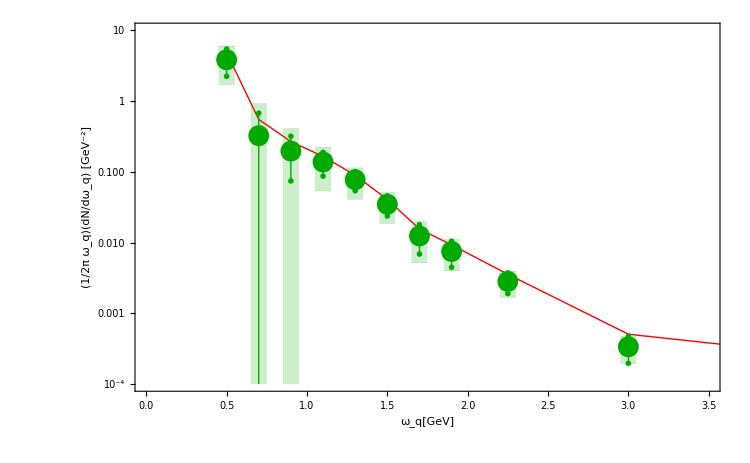

```mathematica
Show[DatDisnp,DatDis,DatSt,DatSy]
```

## Parametros del Modelo.

```mathematica
g:=2;
αs:=1/π;
αem := 1/137;
eB={0.0249, 0.0176, 0.0253, 0.0192, 0.031}; (*i*)
VolT ={450.47, 383.875, 310.03, 256.823, 165.179}; (*j*)
AnchoDisco = 0.25/0.197; (* Esfera de diametro 12fm con contraccion de Lorentz*)
eq={2/3,1/3,1/3}; (*k*)
(*T=1.5/(.197); Δr=7/(.197);χ=.8;R=7/(.197);*)
```

## Expresiones

```mathematica
n[ωp_,Λs_,m_,η_,β_]:=η/(Exp[(√(m^2+ ωp^2(1-β )^2/(1-β^2)))/Λs]-1);
```

```mathematica
dNdq[i_,j_,k_,Λs_,m_,η_,ωq_,β_]:=AnchoDisco* VolT[[j]](αem*αs^2)/(2*(2π)^6)eq[[k]]^2 π  NIntegrate[ⅇ^(-(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eq[[k]] eB[[i]])) (2 ωp^2- ωp ωq+ ωq^2)/ωq(1-β )^2/(1-β^2)(BesselI[0,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB[[i]] eq[[k]])]-BesselI[1,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB[[i]] eq[[k]])])n[ωp,Λs,m,η,β] n[ωq-ωp,Λs,m,η,β],{ωp,0,ωq}];
(*Expresión para el yield, donde ya se hizo la integral sobre theta.*)
```

```mathematica
V2[i_,j_,k_,Λs_,m_,η_,β_,q_]:=AnchoDisco* VolT[[j]](αem*αs^2)/(2*(2π)^5)π eq[[k]]^2 NIntegrate[NIntegrate[ⅇ^(-(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB[[i]] eq[[k]]))( 2 ωp^2-ωp ωq+ ωq^2)(1-β )^2/(1-β^2)(BesselI[0,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB[[i]] eq[[k]])]-(1+(1-β )^2/(1-β^2)(ωp^2-ωp ωq+ωq^2)/(2 eB[[i]] eq[[k]]))/((1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB[[i]] eq[[k]]))BesselI[1,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB[[i]]eq[[k]])])n[ωp,Λs,m,η,β] n[ωq-ωp,Λs,m,η,β],{ωp,0,ωq}],{ωq,0,q}];
(*Expresión para el V2, donde ya se hizo la integral sobre theta.*)
```

```mathematica
NN[i_,j_,k_,Λs_,m_,η_,β_]:=AnchoDisco* VolT[[j]](αem*αs^2)/(2*(2π)^6)π eq[[k]]^2 NIntegrate[NIntegrate[ⅇ^(-(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eq[[k]] eB[[i]])) (2 ωp^2-ωp ωq+ ωq^2) (1-β )^2/(1-β^2)(BesselI[0,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB[[i]] eq[[k]])]-BesselI[1,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB[[i]]eq[[k]])])n[ωp,Λs,m,η,β] n[ωq-ωp,Λs,m,η,β],{ωp,0,ωq}],{ωq,0.2,4}];
(*Integral para N, para la normalización*)
```

### Modificar parametros de λ, μ, η, β

```mathematica
λ=2;μ=10^-15;η=3;β=.25;
```

### Normalizacion

```mathematica
N1=Quiet[NN[1,1,1,λ,μ,η,β]+2NN[1,1,2,λ,μ,η,β]](*Normalización para campo magnetico con la primera entrada del arreglo de eB*)
N2=Quiet[NN[2,2,1,λ,μ,η,β]+2NN[2,2,2,λ,μ,η,β]]
(*Normalización para campo magnetico con la segunda entrada del arreglo de eB*)
```

0.000270666

0.000135382

```mathematica
N3=Quiet[NN[3,3,1,λ,μ,η,β]+2NN[3,3,2,λ,μ,η,β]]
N4=Quiet[NN[4,4,1,λ,μ,η,β]+2NN[4,4,2,λ,μ,η,β]]
N5=Quiet[NN[5,5,1,λ,μ,η,β]+2NN[5,5,2,λ,μ,η,β]]
```

0.000190747

0.000103655

0.000136825

```mathematica
N1=0.00027066646415701336;
```

```mathematica
N2=0.00013538182967851823;
```

```mathematica
N3 = 0.00019074701421108154;
```

```mathematica
N4= 0.00010365467277456576;
N5= 0.0001368251790935933;
```

## Construyendo v2<--- status de modificacion

```mathematica
ListV21eB=Table[{ωq,1/(1+Hy[ωq]/N1eB[ωq])(V2[1eB,1,λ,μ,η,ωq,β]+2V2[1eB,2,λ,μ,η,ωq,β])/N1},{ωq,.3,3.5,.1}]
```

{{0.3,1/(1+4.2077/N1eB[0.3])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.3,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.3,0.25])},{0.4,1/(1+5.95211/N1eB[0.4])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.4,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.4,0.25])},{0.5,1/(1+6.85217/N1eB[0.5])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.5,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.5,0.25])},{0.6,1/(1+7.37461/N1eB[0.6])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.6,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.6,0.25])},{0.7,1/(1+7.69819/N1eB[0.7])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.7,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.7,0.25])},{0.8,1/(1+7.9069/N1eB[0.8])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.8,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.8,0.25])},{0.9,1/(1+8.04542/N1eB[0.9])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.9,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.9,0.25])},{1.,1/(1+8.13938/N1eB[1.])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.,0.25])},{1.1,1/(1+8.20425/N1eB[1.1])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.1,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.1,0.25])},{1.2,1/(1+8.24973/N1eB[1.2])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.2,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.2,0.25])},{1.3,1/(1+8.28205/N1eB[1.3])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.3,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.3,0.25])},{1.4,1/(1+8.3053/N1eB[1.4])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.4,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.4,0.25])},{1.5,1/(1+8.3222/N1eB[1.5])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.5,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.5,0.25])},{1.6,1/(1+8.33463/N1eB[1.6])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.6,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.6,0.25])},{1.7,1/(1+8.34386/N1eB[1.7])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.7,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.7,0.25])},{1.8,1/(1+8.35078/N1eB[1.8])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.8,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.8,0.25])},{1.9,1/(1+8.35602/N1eB[1.9])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.9,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.9,0.25])},{2.,1/(1+8.36002/N1eB[2.])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.,0.25])},{2.1,1/(1+8.36311/N1eB[2.1])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.1,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.1,0.25])},{2.2,1/(1+8.36551/N1eB[2.2])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.2,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.2,0.25])},{2.3,1/(1+8.3674/N1eB[2.3])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.3,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.3,0.25])},{2.4,1/(1+8.3689/N1eB[2.4])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.4,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.4,0.25])},{2.5,1/(1+8.3701/N1eB[2.5])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.5,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.5,0.25])},{2.6,1/(1+8.37107/N1eB[2.6])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.6,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.6,0.25])},{2.7,1/(1+8.37187/N1eB[2.7])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.7,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.7,0.25])},{2.8,1/(1+8.37252/N1eB[2.8])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.8,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.8,0.25])},{2.9,1/(1+8.37305/N1eB[2.9])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.9,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.9,0.25])},{3.,1/(1+8.3735/N1eB[3.])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.,0.25])},{3.1,1/(1+8.37388/N1eB[3.1])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.1,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.1,0.25])},{3.2,1/(1+8.37419/N1eB[3.2])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.2,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.2,0.25])},{3.3,1/(1+8.37446/N1eB[3.3])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.3,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.3,0.25])},{3.4,1/(1+8.37469/N1eB[3.4])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.4,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.4,0.25])},{3.5,1/(1+8.37488/N1eB[3.5])3694.58 (V2[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.5,0.25]+2 V2[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.5,0.25])}}

```mathematica
ListV21eB={{0.3,0.09216885873389785},{0.4,0.08005381174811935},{0.5,0.06801656936472852},{0.6000000000000001,0.05894211045976697},{0.7,0.0521650744623796},{0.8,0.046898387302108754},{0.9000000000000001,0.04284987706548468},{1.,0.039510082238175086},{1.1,0.036727821575081164},{1.2,0.03443929970186223},{1.3,0.03268260773550342},{1.4000000000000001,0.031105761902686595},{1.5000000000000002,0.02982057940799103},{1.6,0.028531591352385758},{1.7000000000000002,0.027554868475410613},{1.8,0.026644825007248858},{1.9000000000000001,0.025836599515602514},{2.,0.02498684493380116},{2.1,0.024507820680845383},{2.2,0.02399540211727979},{2.3,0.023392446404182074},{2.4,0.022865690263047363},{2.5,0.022584270868624308},{2.6,0.022109533438561556},{2.7,0.021727864871781966},{2.8,0.02148411366704191},{2.9,0.02132052249419074},{3.,0.020996446545497684},{3.1,0.02084848500119532},{3.2,0.02052123405228317},{3.3,0.020293376726744396},{3.4,0.020187202635680652},{3.5,0.019974087038467037}}
```

{{0.3,0.0921689},{0.4,0.0800538},{0.5,0.0680166},{0.6,0.0589421},{0.7,0.0521651},{0.8,0.0468984},{0.9,0.0428499},{1.,0.0395101},{1.1,0.0367278},{1.2,0.0344393},{1.3,0.0326826},{1.4,0.0311058},{1.5,0.0298206},{1.6,0.0285316},{1.7,0.0275549},{1.8,0.0266448},{1.9,0.0258366},{2.,0.0249868},{2.1,0.0245078},{2.2,0.0239954},{2.3,0.0233924},{2.4,0.0228657},{2.5,0.0225843},{2.6,0.0221095},{2.7,0.0217279},{2.8,0.0214841},{2.9,0.0213205},{3.,0.0209964},{3.1,0.0208485},{3.2,0.0205212},{3.3,0.0202934},{3.4,0.0201872},{3.5,0.0199741}}

```mathematica
ListV21eB={{0.3,0.054372056347015724},{0.4,0.043893594805702124},{0.5,0.03677710341480918},{0.6000000000000001,0.031832628895322845},{0.7,0.02828135529587229},{0.8,0.02562231662153532},{0.9000000000000001,0.02352702380527038},{1.,0.021845613951159932},{1.1,0.02055711266619647},{1.2,0.01941545755222691},{1.3,0.018559278480418134},{1.4000000000000001,0.01778352787279217},{1.5000000000000002,0.017123969187247533},{1.6,0.016520507952598892},{1.7000000000000002,0.016127602958852287},{1.8,0.015691062486996882},{1.9000000000000001,0.015364529514656436},{2.,0.014930884777284036},{2.1,0.014702435237572784},{2.2,0.0144254243441667},{2.3,0.014121656418161092},{2.4,0.01396522807606012},{2.5,0.01379186252652981},{2.6,0.013681378376942204},{2.7,0.013503819703078703},{2.8,0.01338237968955044},{2.9,0.013261442702911404},{3.,0.013160437964522232},{3.1,0.01301429004917571},{3.2,0.012922585034635566},{3.3,0.012852670275296421},{3.4,0.012813980434872632},{3.5,0.012782500223086876}}(*sin flujo*)
```

{{0.3,0.0543721},{0.4,0.0438936},{0.5,0.0367771},{0.6,0.0318326},{0.7,0.0282814},{0.8,0.0256223},{0.9,0.023527},{1.,0.0218456},{1.1,0.0205571},{1.2,0.0194155},{1.3,0.0185593},{1.4,0.0177835},{1.5,0.017124},{1.6,0.0165205},{1.7,0.0161276},{1.8,0.0156911},{1.9,0.0153645},{2.,0.0149309},{2.1,0.0147024},{2.2,0.0144254},{2.3,0.0141217},{2.4,0.0139652},{2.5,0.0137919},{2.6,0.0136814},{2.7,0.0135038},{2.8,0.0133824},{2.9,0.0132614},{3.,0.0131604},{3.1,0.0130143},{3.2,0.0129226},{3.3,0.0128527},{3.4,0.012814},{3.5,0.0127825}}

```mathematica
ListV23eB=Table[{ωq,1/(1+Hy[ωq]/N3eB[ωq])(V2[3eB,1,λ,μ,η,ωq,β]+2V2[3eB,2,λ,μ,η,ωq,β])/N3},{ωq,.3,3.5,.1}]
```

{{0.3,1/(1+4.2077/N3eB[0.3])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.3,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.3,0.25])},{0.4,1/(1+5.95211/N3eB[0.4])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.4,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.4,0.25])},{0.5,1/(1+6.85217/N3eB[0.5])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.5,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.5,0.25])},{0.6,1/(1+7.37461/N3eB[0.6])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.6,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.6,0.25])},{0.7,1/(1+7.69819/N3eB[0.7])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.7,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.7,0.25])},{0.8,1/(1+7.9069/N3eB[0.8])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.8,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.8,0.25])},{0.9,1/(1+8.04542/N3eB[0.9])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.9,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.9,0.25])},{1.,1/(1+8.13938/N3eB[1.])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.,0.25])},{1.1,1/(1+8.20425/N3eB[1.1])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.1,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.1,0.25])},{1.2,1/(1+8.24973/N3eB[1.2])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.2,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.2,0.25])},{1.3,1/(1+8.28205/N3eB[1.3])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.3,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.3,0.25])},{1.4,1/(1+8.3053/N3eB[1.4])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.4,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.4,0.25])},{1.5,1/(1+8.3222/N3eB[1.5])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.5,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.5,0.25])},{1.6,1/(1+8.33463/N3eB[1.6])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.6,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.6,0.25])},{1.7,1/(1+8.34386/N3eB[1.7])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.7,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.7,0.25])},{1.8,1/(1+8.35078/N3eB[1.8])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.8,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.8,0.25])},{1.9,1/(1+8.35602/N3eB[1.9])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.9,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.9,0.25])},{2.,1/(1+8.36002/N3eB[2.])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.,0.25])},{2.1,1/(1+8.36311/N3eB[2.1])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.1,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.1,0.25])},{2.2,1/(1+8.36551/N3eB[2.2])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.2,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.2,0.25])},{2.3,1/(1+8.3674/N3eB[2.3])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.3,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.3,0.25])},{2.4,1/(1+8.3689/N3eB[2.4])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.4,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.4,0.25])},{2.5,1/(1+8.3701/N3eB[2.5])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.5,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.5,0.25])},{2.6,1/(1+8.37107/N3eB[2.6])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.6,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.6,0.25])},{2.7,1/(1+8.37187/N3eB[2.7])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.7,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.7,0.25])},{2.8,1/(1+8.37252/N3eB[2.8])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.8,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.8,0.25])},{2.9,1/(1+8.37305/N3eB[2.9])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.9,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.9,0.25])},{3.,1/(1+8.3735/N3eB[3.])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.,0.25])},{3.1,1/(1+8.37388/N3eB[3.1])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.1,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.1,0.25])},{3.2,1/(1+8.37419/N3eB[3.2])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.2,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.2,0.25])},{3.3,1/(1+8.37446/N3eB[3.3])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.3,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.3,0.25])},{3.4,1/(1+8.37469/N3eB[3.4])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.4,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.4,0.25])},{3.5,1/(1+8.37488/N3eB[3.5])7386.52 (V2[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.5,0.25]+2 V2[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.5,0.25])}}

```mathematica
{{0.3,0.12785145572543424},{0.4,0.13309991572144325},{0.5,0.12197264634669926},{0.6000000000000001,0.10901774607664537},{0.7,0.09782003012833607},{0.8,0.08851987896596729},{0.9000000000000001,0.08132233561752386},{1.,0.0753773498332943},{1.1,0.07050133905108148},{1.2,0.06637399154971343},{1.3,0.06312342178160923},{1.4000000000000001,0.06002517372923297},{1.5000000000000002,0.05782446135790718},{1.6,0.055555889989001},{1.7000000000000002,0.05377747467155102},{1.8,0.05223940108634164},{1.9000000000000001,0.05086573750614938},{2.,0.04959832463066053},{2.1,0.04870281374717331},{2.2,0.04762403448250061},{2.3,0.046806143670735004},{2.4,0.04611803937717221},{2.5,0.045418415901431336},{2.6,0.04494782670677493},{2.7,0.044217738566168084},{2.8,0.04377000462472917},{2.9,0.043284479577678545},{3.,0.04278862778390341},{3.1,0.04235121407688494},{3.2,0.04215587880056952},{3.3,0.04182282254730269},{3.4,0.04192014112706865},{3.5,0.04138267662006927}}(*Sin Flujo*)
```

{{0.3,0.127851},{0.4,0.1331},{0.5,0.121973},{0.6,0.109018},{0.7,0.09782},{0.8,0.0885199},{0.9,0.0813223},{1.,0.0753773},{1.1,0.0705013},{1.2,0.066374},{1.3,0.0631234},{1.4,0.0600252},{1.5,0.0578245},{1.6,0.0555559},{1.7,0.0537775},{1.8,0.0522394},{1.9,0.0508657},{2.,0.0495983},{2.1,0.0487028},{2.2,0.047624},{2.3,0.0468061},{2.4,0.046118},{2.5,0.0454184},{2.6,0.0449478},{2.7,0.0442177},{2.8,0.04377},{2.9,0.0432845},{3.,0.0427886},{3.1,0.0423512},{3.2,0.0421559},{3.3,0.0418228},{3.4,0.0419201},{3.5,0.0413827}}

```mathematica
ListV23eB={{0.30000000000000004,5.038323176361645},{0.4,5.2451525588513315},{0.5,4.806653217077793},{0.6000000000000001,4.296131268714231},{0.7000000000000001,3.8548557942617516},{0.8,3.4883588554575735},{0.9,3.204720712586466},{1.,2.9704428978375352},{1.1,2.778290857074148},{1.2000000000000002,2.6156418637165846},{1.3,2.4875446050182477},{1.4000000000000001,2.3654499845085866},{1.5,2.278725120235095},{1.6,2.1893260935260344},{1.7000000000000002,2.1192429563394914},{1.8,2.058631117801243},{1.9000000000000001,2.004498288313015},{2.,1.9545525475440715},{2.1,1.9192625837860748},{2.2,1.876750447021271},{2.3000000000000003,1.8445193065209904},{2.4000000000000004,1.8174027454279618},{2.5,1.7898322406374512},{2.6,1.7712874346160425},{2.7,1.742516389509558},{2.8000000000000003,1.724872254906665},{2.9000000000000004,1.7057388623036691},{3.,1.686198517061274},{3.1,1.6689610784632944},{3.2,1.6612633776883072},{3.3000000000000003,1.6481384192719553},{3.4000000000000004,1.6519735140946408},{3.5,1.6307933103439525},{3.6,1.6176063509904233},{3.7,1.610198089675887},{3.8000000000000003,1.6053991357357285},{3.9000000000000004,1.5941668486292038},{4.,1.591263658477583}};
```

```mathematica
v21eB=Interpolation[ListV21eB]
v23eB=Interpolation[ListV23eB]
```

InterpolatingFunction[{{0.3, 3.5}}, <>]

InterpolatingFunction[{{0.3, 4.}}, <>]

```mathematica
v21eB[.4]
```

0.0438936

```mathematica
dN1eB=Evaluate[Table[{.02i,dNdq[eB,1,λ,μ,η,.02i,β]+2dNdq[eB,2,λ,μ,η,.02i,β]},{i,10,200}]](*Tabla de datos del yield para una vez la masa de pión*)
```

{{0.2,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.2,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.2,0.25]},{0.22,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.22,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.22,0.25]},{0.24,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.24,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.24,0.25]},{0.26,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.26,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.26,0.25]},{0.28,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.28,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.28,0.25]},{0.3,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.3,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.3,0.25]},{0.32,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.32,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.32,0.25]},{0.34,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.34,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.34,0.25]},{0.36,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.36,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.36,0.25]},{0.38,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.38,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.38,0.25]},{0.4,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.4,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.4,0.25]},{0.42,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.42,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.42,0.25]},{0.44,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.44,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.44,0.25]},{0.46,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.46,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.46,0.25]},{0.48,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.48,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.48,0.25]},{0.5,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.5,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.5,0.25]},{0.52,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.52,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.52,0.25]},{0.54,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.54,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.54,0.25]},{0.56,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.56,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.56,0.25]},{0.58,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.58,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.58,0.25]},{0.6,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.6,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.6,0.25]},{0.62,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.62,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.62,0.25]},{0.64,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.64,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.64,0.25]},{0.66,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.66,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.66,0.25]},{0.68,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.68,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.68,0.25]},{0.7,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.7,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.7,0.25]},{0.72,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.72,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.72,0.25]},{0.74,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.74,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.74,0.25]},{0.76,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.76,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.76,0.25]},{0.78,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.78,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.78,0.25]},{0.8,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.8,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.8,0.25]},{0.82,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.82,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.82,0.25]},{0.84,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.84,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.84,0.25]},{0.86,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.86,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.86,0.25]},{0.88,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.88,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.88,0.25]},{0.9,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.9,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.9,0.25]},{0.92,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.92,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.92,0.25]},{0.94,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.94,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.94,0.25]},{0.96,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.96,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.96,0.25]},{0.98,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,0.98,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,0.98,0.25]},{1.,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.,0.25]},{1.02,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.02,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.02,0.25]},{1.04,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.04,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.04,0.25]},{1.06,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.06,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.06,0.25]},{1.08,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.08,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.08,0.25]},{1.1,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.1,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.1,0.25]},{1.12,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.12,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.12,0.25]},{1.14,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.14,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.14,0.25]},{1.16,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.16,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.16,0.25]},{1.18,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.18,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.18,0.25]},{1.2,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.2,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.2,0.25]},{1.22,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.22,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.22,0.25]},{1.24,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.24,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.24,0.25]},{1.26,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.26,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.26,0.25]},{1.28,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.28,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.28,0.25]},{1.3,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.3,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.3,0.25]},{1.32,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.32,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.32,0.25]},{1.34,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.34,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.34,0.25]},{1.36,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.36,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.36,0.25]},{1.38,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.38,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.38,0.25]},{1.4,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.4,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.4,0.25]},{1.42,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.42,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.42,0.25]},{1.44,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.44,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.44,0.25]},{1.46,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.46,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.46,0.25]},{1.48,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.48,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.48,0.25]},{1.5,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.5,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.5,0.25]},{1.52,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.52,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.52,0.25]},{1.54,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.54,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.54,0.25]},{1.56,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.56,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.56,0.25]},{1.58,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.58,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.58,0.25]},{1.6,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.6,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.6,0.25]},{1.62,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.62,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.62,0.25]},{1.64,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.64,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.64,0.25]},{1.66,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.66,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.66,0.25]},{1.68,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.68,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.68,0.25]},{1.7,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.7,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.7,0.25]},{1.72,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.72,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.72,0.25]},{1.74,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.74,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.74,0.25]},{1.76,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.76,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.76,0.25]},{1.78,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.78,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.78,0.25]},{1.8,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.8,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.8,0.25]},{1.82,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.82,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.82,0.25]},{1.84,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.84,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.84,0.25]},{1.86,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.86,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.86,0.25]},{1.88,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.88,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.88,0.25]},{1.9,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.9,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.9,0.25]},{1.92,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.92,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.92,0.25]},{1.94,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.94,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.94,0.25]},{1.96,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.96,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.96,0.25]},{1.98,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,1.98,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,1.98,0.25]},{2.,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.,0.25]},{2.02,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.02,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.02,0.25]},{2.04,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.04,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.04,0.25]},{2.06,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.06,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.06,0.25]},{2.08,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.08,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.08,0.25]},{2.1,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.1,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.1,0.25]},{2.12,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.12,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.12,0.25]},{2.14,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.14,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.14,0.25]},{2.16,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.16,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.16,0.25]},{2.18,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.18,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.18,0.25]},{2.2,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.2,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.2,0.25]},{2.22,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.22,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.22,0.25]},{2.24,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.24,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.24,0.25]},{2.26,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.26,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.26,0.25]},{2.28,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.28,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.28,0.25]},{2.3,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.3,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.3,0.25]},{2.32,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.32,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.32,0.25]},{2.34,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.34,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.34,0.25]},{2.36,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.36,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.36,0.25]},{2.38,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.38,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.38,0.25]},{2.4,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.4,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.4,0.25]},{2.42,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.42,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.42,0.25]},{2.44,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.44,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.44,0.25]},{2.46,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.46,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.46,0.25]},{2.48,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.48,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.48,0.25]},{2.5,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.5,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.5,0.25]},{2.52,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.52,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.52,0.25]},{2.54,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.54,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.54,0.25]},{2.56,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.56,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.56,0.25]},{2.58,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.58,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.58,0.25]},{2.6,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.6,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.6,0.25]},{2.62,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.62,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.62,0.25]},{2.64,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.64,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.64,0.25]},{2.66,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.66,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.66,0.25]},{2.68,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.68,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.68,0.25]},{2.7,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.7,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.7,0.25]},{2.72,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.72,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.72,0.25]},{2.74,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.74,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.74,0.25]},{2.76,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.76,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.76,0.25]},{2.78,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.78,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.78,0.25]},{2.8,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.8,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.8,0.25]},{2.82,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.82,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.82,0.25]},{2.84,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.84,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.84,0.25]},{2.86,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.86,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.86,0.25]},{2.88,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.88,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.88,0.25]},{2.9,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.9,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.9,0.25]},{2.92,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.92,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.92,0.25]},{2.94,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.94,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.94,0.25]},{2.96,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.96,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.96,0.25]},{2.98,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,2.98,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,2.98,0.25]},{3.,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.,0.25]},{3.02,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.02,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.02,0.25]},{3.04,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.04,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.04,0.25]},{3.06,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.06,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.06,0.25]},{3.08,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.08,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.08,0.25]},{3.1,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.1,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.1,0.25]},{3.12,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.12,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.12,0.25]},{3.14,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.14,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.14,0.25]},{3.16,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.16,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.16,0.25]},{3.18,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.18,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.18,0.25]},{3.2,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.2,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.2,0.25]},{3.22,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.22,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.22,0.25]},{3.24,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.24,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.24,0.25]},{3.26,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.26,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.26,0.25]},{3.28,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.28,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.28,0.25]},{3.3,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.3,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.3,0.25]},{3.32,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.32,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.32,0.25]},{3.34,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.34,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.34,0.25]},{3.36,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.36,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.36,0.25]},{3.38,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.38,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.38,0.25]},{3.4,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.4,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.4,0.25]},{3.42,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.42,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.42,0.25]},{3.44,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.44,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.44,0.25]},{3.46,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.46,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.46,0.25]},{3.48,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.48,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.48,0.25]},{3.5,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.5,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.5,0.25]},{3.52,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.52,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.52,0.25]},{3.54,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.54,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.54,0.25]},{3.56,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.56,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.56,0.25]},{3.58,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.58,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.58,0.25]},{3.6,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.6,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.6,0.25]},{3.62,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.62,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.62,0.25]},{3.64,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.64,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.64,0.25]},{3.66,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.66,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.66,0.25]},{3.68,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.68,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.68,0.25]},{3.7,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.7,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.7,0.25]},{3.72,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.72,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.72,0.25]},{3.74,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.74,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.74,0.25]},{3.76,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.76,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.76,0.25]},{3.78,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.78,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.78,0.25]},{3.8,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.8,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.8,0.25]},{3.82,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.82,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.82,0.25]},{3.84,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.84,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.84,0.25]},{3.86,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.86,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.86,0.25]},{3.88,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.88,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.88,0.25]},{3.9,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.9,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.9,0.25]},{3.92,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.92,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.92,0.25]},{3.94,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.94,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.94,0.25]},{3.96,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.96,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.96,0.25]},{3.98,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,3.98,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,3.98,0.25]},{4.,dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},1,2,1/1000000000000000,3,4.,0.25]+2 dNdq[{0.0249,0.0176,0.0253,0.0192,0.031},2,2,1/1000000000000000,3,4.,0.25]}}

```mathematica
{{0.2,5.392293372819496},{0.22,3.9758825491948944},{0.24,2.9528968737901926},{0.26,2.2414250565447613},{0.28,1.7248392157828518},{0.3,1.3548387730220524},{0.32,1.090148931164546},{0.34,0.8927819459312829},{0.36,0.7446104074294717},{0.38,0.6184205018330063},{0.4,0.5212259473596416},{0.42,0.44696077367524645},{0.44,0.3829348821994843},{0.46,0.33382537729030604},{0.48,0.2904507997958827},{0.5,0.2553296527572159},{0.52,0.22515815542018847},{0.54,0.20016781833224562},{0.56,0.1779947574509888},{0.58,0.1595861475278662},{0.6,0.14321745546491607},{0.62,0.12904053685800568},{0.64,0.11663577232984121},{0.66,0.10893782713238571},{0.68,0.0960093119828413},{0.7000000000000001,0.08790177056411587},{0.72,0.08324029693805052},{0.74,0.0764739727353707},{0.76,0.06722077939288436},{0.78,0.06194348505936371},{0.8,0.0585699495509172},{0.8200000000000001,0.052741567270018545},{0.84,0.048733340563214926},{0.86,0.045151438336009694},{0.88,0.04205847648002389},{0.9,0.039123929506024},{0.92,0.03637008771412512},{0.9400000000000001,0.03397213131808022},{0.96,0.031670512741656644},{0.98,0.029637360124120674},{1.,0.027761285328863544},{1.02,0.025994255840119707},{1.04,0.024429063295824366},{1.06,0.022939647547780627},{1.08,0.02161235410152218},{1.1,0.020288156011235167},{1.12,0.019137956819936013},{1.1400000000000001,0.018078490794624244},{1.16,0.017047346682226835},{1.18,0.01610952808006384},{1.2,0.015241347710317349},{1.22,0.014437815869948802},{1.24,0.013625152840268547},{1.26,0.01291327205544998},{1.28,0.012270426367845182},{1.3,0.011643294537211581},{1.32,0.011077319338498115},{1.34,0.010525080666530486},{1.36,0.010017234342404754},{1.3800000000000001,0.009549801304272828},{1.4000000000000001,0.009095293671772748},{1.42,0.008679690595459661},{1.44,0.008276755863762062},{1.46,0.007909148710260315},{1.48,0.007554057020488489},{1.5,0.007205134995043086},{1.52,0.0068958689776421065},{1.54,0.006597355269260687},{1.56,0.0063179098687718115},{1.58,0.006056223099212774},{1.6,0.005798785220077593},{1.62,0.005563240864999688},{1.6400000000000001,0.0053351957592734835},{1.6600000000000001,0.005111997083531289},{1.68,0.004878828937423107},{1.7,0.004684575486429266},{1.72,0.004499778363920501},{1.74,0.004322048889995267},{1.76,0.004158183266149177},{1.78,0.003999904313449024},{1.8,0.003847851850448129},{1.82,0.0036424420581899876},{1.84,0.0035070703314158346},{1.86,0.0033807030058366355},{1.8800000000000001,0.0033087539838806473},{1.9000000000000001,0.0031887955718927726},{1.92,0.0030750672018615686},{1.94,0.0029633601187340724},{1.96,0.0028602586200147744},{1.98,0.0027583128976327877},{2.,0.002662247731347155},{2.02,0.002564585399864133},{2.04,0.0024785076007166748},{2.06,0.002394372177566235},{2.08,0.002314046068736128},{2.1,0.002236707385237681},{2.12,0.0021631344101282575},{2.14,0.002093440613166032},{2.16,0.0020247012529810136},{2.18,0.0019578710202132047},{2.2,0.001894765406113031},{2.22,0.0018347976114854645},{2.24,0.001775338009370054},{2.2600000000000002,0.0017203671533567023},{2.2800000000000002,0.0016669819819876011},{2.3000000000000003,0.0016152075837130037},{2.32,0.0015657814314062606},{2.34,0.0015165299889391033},{2.36,0.0014705741113216},{2.38,0.0014237327453318262},{2.4,0.0013808751385804465},{2.42,0.0013400362589335913},{2.44,0.0013000952502750106},{2.46,0.001258053163762697},{2.48,0.0012211465189143277},{2.5,0.0011756791572981634},{2.52,0.0011403536277385246},{2.54,0.0011058062402903445},{2.56,0.0010745053176423088},{2.58,0.0010447121840892954},{2.6,0.0010147566013953958},{2.62,0.0009869723839479887},{2.64,0.0009580889203920514},{2.66,0.000931661942975065},{2.68,0.0009058292751120611},{2.7,0.0008806135759577601},{2.72,0.0008557457971320549},{2.74,0.0008322022389125646},{2.7600000000000002,0.0008101012711272631},{2.7800000000000002,0.00078849005653689},{2.8000000000000003,0.0007670865905165198},{2.82,0.0007464053403438562},{2.84,0.0007264146100220307},{2.86,0.00070761495245312},{2.88,0.0006888629768470979},{2.9,0.0006691289967856406},{2.92,0.0006520727158882929},{2.94,0.0006347208049165472},{2.96,0.0006184949537988583},{2.98,0.000602098929593526},{3.,0.0005869660981740507},{3.02,0.0005723627451575915},{3.04,0.0005577720324059439},{3.06,0.0005471782708782575},{3.08,0.0005336264420502746},{3.1,0.0005203125105192732},{3.12,0.0005075347258058924},{3.14,0.0004950070931979328},{3.16,0.00047858511027317613},{3.18,0.0004676027551888326},{3.2,0.0004559229692964922},{3.22,0.0004450828182045154},{3.24,0.00043424137683737216},{3.2600000000000002,0.00042400618006936956},{3.2800000000000002,0.00041359604276203953},{3.3000000000000003,0.00040368707194294196},{3.3200000000000003,0.00039419923803432394},{3.34,0.0003835581984973566},{3.36,0.00037467298568256215},{3.38,0.0003658931695764919},{3.4,0.0003568150712366712},{3.42,0.0003483677673093549},{3.44,0.00034035685875403234},{3.46,0.00033243583940866975},{3.48,0.0003247104273537736},{3.5,0.00031741527566280284},{3.52,0.0003101700779014606},{3.54,0.000303159292621452},{3.56,0.00029641789719235556},{3.58,0.00028967146280421723},{3.6,0.00028327788881536323},{3.62,0.00027679232164167953},{3.64,0.0002705361548451635},{3.66,0.00026463889773650225},{3.68,0.00025871749080342974},{3.7,0.0002531183031163891},{3.72,0.0002475505978681837},{3.74,0.00024179062421535955},{3.7600000000000002,0.0002366007528044174},{3.7800000000000002,0.00023128869036356518},{3.8000000000000003,0.00022589082601345611},{3.8200000000000003,0.00022099747692209037},{3.84,0.00021627147858017235},{3.86,0.0002117157763504483},{3.88,0.00020706028882609988},{3.9,0.0002027272181345722},{3.92,0.00019836052484814627},{3.94,0.00019414005654660348},{3.96,0.000190109535030641},{3.98,0.0001860736761788127},{4.,0.00018222190925914269}}(*Sin Flujo*)
```

{{0.2,5.39229},{0.22,3.97588},{0.24,2.9529},{0.26,2.24143},{0.28,1.72484},{0.3,1.35484},{0.32,1.09015},{0.34,0.892782},{0.36,0.74461},{0.38,0.618421},{0.4,0.521226},{0.42,0.446961},{0.44,0.382935},{0.46,0.333825},{0.48,0.290451},{0.5,0.25533},{0.52,0.225158},{0.54,0.200168},{0.56,0.177995},{0.58,0.159586},{0.6,0.143217},{0.62,0.129041},{0.64,0.116636},{0.66,0.108938},{0.68,0.0960093},{0.7,0.0879018},{0.72,0.0832403},{0.74,0.076474},{0.76,0.0672208},{0.78,0.0619435},{0.8,0.0585699},{0.82,0.0527416},{0.84,0.0487333},{0.86,0.0451514},{0.88,0.0420585},{0.9,0.0391239},{0.92,0.0363701},{0.94,0.0339721},{0.96,0.0316705},{0.98,0.0296374},{1.,0.0277613},{1.02,0.0259943},{1.04,0.0244291},{1.06,0.0229396},{1.08,0.0216124},{1.1,0.0202882},{1.12,0.019138},{1.14,0.0180785},{1.16,0.0170473},{1.18,0.0161095},{1.2,0.0152413},{1.22,0.0144378},{1.24,0.0136252},{1.26,0.0129133},{1.28,0.0122704},{1.3,0.0116433},{1.32,0.0110773},{1.34,0.0105251},{1.36,0.0100172},{1.38,0.0095498},{1.4,0.00909529},{1.42,0.00867969},{1.44,0.00827676},{1.46,0.00790915},{1.48,0.00755406},{1.5,0.00720513},{1.52,0.00689587},{1.54,0.00659736},{1.56,0.00631791},{1.58,0.00605622},{1.6,0.00579879},{1.62,0.00556324},{1.64,0.0053352},{1.66,0.005112},{1.68,0.00487883},{1.7,0.00468458},{1.72,0.00449978},{1.74,0.00432205},{1.76,0.00415818},{1.78,0.0039999},{1.8,0.00384785},{1.82,0.00364244},{1.84,0.00350707},{1.86,0.0033807},{1.88,0.00330875},{1.9,0.0031888},{1.92,0.00307507},{1.94,0.00296336},{1.96,0.00286026},{1.98,0.00275831},{2.,0.00266225},{2.02,0.00256459},{2.04,0.00247851},{2.06,0.00239437},{2.08,0.00231405},{2.1,0.00223671},{2.12,0.00216313},{2.14,0.00209344},{2.16,0.0020247},{2.18,0.00195787},{2.2,0.00189477},{2.22,0.0018348},{2.24,0.00177534},{2.26,0.00172037},{2.28,0.00166698},{2.3,0.00161521},{2.32,0.00156578},{2.34,0.00151653},{2.36,0.00147057},{2.38,0.00142373},{2.4,0.00138088},{2.42,0.00134004},{2.44,0.0013001},{2.46,0.00125805},{2.48,0.00122115},{2.5,0.00117568},{2.52,0.00114035},{2.54,0.00110581},{2.56,0.00107451},{2.58,0.00104471},{2.6,0.00101476},{2.62,0.000986972},{2.64,0.000958089},{2.66,0.000931662},{2.68,0.000905829},{2.7,0.000880614},{2.72,0.000855746},{2.74,0.000832202},{2.76,0.000810101},{2.78,0.00078849},{2.8,0.000767087},{2.82,0.000746405},{2.84,0.000726415},{2.86,0.000707615},{2.88,0.000688863},{2.9,0.000669129},{2.92,0.000652073},{2.94,0.000634721},{2.96,0.000618495},{2.98,0.000602099},{3.,0.000586966},{3.02,0.000572363},{3.04,0.000557772},{3.06,0.000547178},{3.08,0.000533626},{3.1,0.000520313},{3.12,0.000507535},{3.14,0.000495007},{3.16,0.000478585},{3.18,0.000467603},{3.2,0.000455923},{3.22,0.000445083},{3.24,0.000434241},{3.26,0.000424006},{3.28,0.000413596},{3.3,0.000403687},{3.32,0.000394199},{3.34,0.000383558},{3.36,0.000374673},{3.38,0.000365893},{3.4,0.000356815},{3.42,0.000348368},{3.44,0.000340357},{3.46,0.000332436},{3.48,0.00032471},{3.5,0.000317415},{3.52,0.00031017},{3.54,0.000303159},{3.56,0.000296418},{3.58,0.000289671},{3.6,0.000283278},{3.62,0.000276792},{3.64,0.000270536},{3.66,0.000264639},{3.68,0.000258717},{3.7,0.000253118},{3.72,0.000247551},{3.74,0.000241791},{3.76,0.000236601},{3.78,0.000231289},{3.8,0.000225891},{3.82,0.000220997},{3.84,0.000216271},{3.86,0.000211716},{3.88,0.00020706},{3.9,0.000202727},{3.92,0.000198361},{3.94,0.00019414},{3.96,0.00019011},{3.98,0.000186074},{4.,0.000182222}}

```mathematica
dN3eB=Evaluate[Table[{.02i,dNdq[3eB,1,λ,μ,η,.02i,β]+2dNdq[3eB,2,λ,μ,η,.02i,β]},{i,10,200}]](*Tabla de datos del yield para 3 veces la masa de pión*)
```

{{0.2,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.2,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.2,0.25]},{0.22,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.22,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.22,0.25]},{0.24,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.24,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.24,0.25]},{0.26,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.26,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.26,0.25]},{0.28,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.28,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.28,0.25]},{0.3,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.3,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.3,0.25]},{0.32,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.32,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.32,0.25]},{0.34,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.34,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.34,0.25]},{0.36,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.36,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.36,0.25]},{0.38,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.38,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.38,0.25]},{0.4,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.4,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.4,0.25]},{0.42,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.42,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.42,0.25]},{0.44,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.44,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.44,0.25]},{0.46,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.46,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.46,0.25]},{0.48,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.48,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.48,0.25]},{0.5,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.5,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.5,0.25]},{0.52,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.52,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.52,0.25]},{0.54,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.54,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.54,0.25]},{0.56,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.56,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.56,0.25]},{0.58,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.58,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.58,0.25]},{0.6,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.6,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.6,0.25]},{0.62,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.62,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.62,0.25]},{0.64,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.64,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.64,0.25]},{0.66,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.66,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.66,0.25]},{0.68,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.68,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.68,0.25]},{0.7,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.7,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.7,0.25]},{0.72,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.72,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.72,0.25]},{0.74,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.74,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.74,0.25]},{0.76,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.76,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.76,0.25]},{0.78,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.78,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.78,0.25]},{0.8,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.8,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.8,0.25]},{0.82,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.82,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.82,0.25]},{0.84,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.84,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.84,0.25]},{0.86,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.86,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.86,0.25]},{0.88,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.88,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.88,0.25]},{0.9,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.9,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.9,0.25]},{0.92,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.92,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.92,0.25]},{0.94,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.94,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.94,0.25]},{0.96,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.96,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.96,0.25]},{0.98,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,0.98,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,0.98,0.25]},{1.,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.,0.25]},{1.02,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.02,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.02,0.25]},{1.04,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.04,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.04,0.25]},{1.06,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.06,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.06,0.25]},{1.08,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.08,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.08,0.25]},{1.1,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.1,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.1,0.25]},{1.12,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.12,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.12,0.25]},{1.14,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.14,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.14,0.25]},{1.16,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.16,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.16,0.25]},{1.18,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.18,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.18,0.25]},{1.2,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.2,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.2,0.25]},{1.22,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.22,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.22,0.25]},{1.24,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.24,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.24,0.25]},{1.26,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.26,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.26,0.25]},{1.28,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.28,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.28,0.25]},{1.3,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.3,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.3,0.25]},{1.32,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.32,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.32,0.25]},{1.34,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.34,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.34,0.25]},{1.36,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.36,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.36,0.25]},{1.38,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.38,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.38,0.25]},{1.4,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.4,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.4,0.25]},{1.42,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.42,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.42,0.25]},{1.44,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.44,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.44,0.25]},{1.46,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.46,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.46,0.25]},{1.48,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.48,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.48,0.25]},{1.5,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.5,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.5,0.25]},{1.52,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.52,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.52,0.25]},{1.54,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.54,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.54,0.25]},{1.56,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.56,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.56,0.25]},{1.58,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.58,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.58,0.25]},{1.6,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.6,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.6,0.25]},{1.62,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.62,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.62,0.25]},{1.64,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.64,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.64,0.25]},{1.66,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.66,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.66,0.25]},{1.68,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.68,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.68,0.25]},{1.7,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.7,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.7,0.25]},{1.72,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.72,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.72,0.25]},{1.74,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.74,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.74,0.25]},{1.76,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.76,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.76,0.25]},{1.78,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.78,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.78,0.25]},{1.8,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.8,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.8,0.25]},{1.82,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.82,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.82,0.25]},{1.84,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.84,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.84,0.25]},{1.86,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.86,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.86,0.25]},{1.88,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.88,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.88,0.25]},{1.9,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.9,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.9,0.25]},{1.92,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.92,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.92,0.25]},{1.94,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.94,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.94,0.25]},{1.96,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.96,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.96,0.25]},{1.98,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,1.98,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,1.98,0.25]},{2.,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.,0.25]},{2.02,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.02,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.02,0.25]},{2.04,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.04,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.04,0.25]},{2.06,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.06,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.06,0.25]},{2.08,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.08,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.08,0.25]},{2.1,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.1,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.1,0.25]},{2.12,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.12,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.12,0.25]},{2.14,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.14,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.14,0.25]},{2.16,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.16,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.16,0.25]},{2.18,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.18,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.18,0.25]},{2.2,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.2,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.2,0.25]},{2.22,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.22,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.22,0.25]},{2.24,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.24,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.24,0.25]},{2.26,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.26,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.26,0.25]},{2.28,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.28,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.28,0.25]},{2.3,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.3,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.3,0.25]},{2.32,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.32,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.32,0.25]},{2.34,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.34,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.34,0.25]},{2.36,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.36,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.36,0.25]},{2.38,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.38,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.38,0.25]},{2.4,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.4,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.4,0.25]},{2.42,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.42,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.42,0.25]},{2.44,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.44,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.44,0.25]},{2.46,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.46,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.46,0.25]},{2.48,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.48,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.48,0.25]},{2.5,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.5,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.5,0.25]},{2.52,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.52,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.52,0.25]},{2.54,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.54,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.54,0.25]},{2.56,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.56,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.56,0.25]},{2.58,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.58,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.58,0.25]},{2.6,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.6,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.6,0.25]},{2.62,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.62,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.62,0.25]},{2.64,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.64,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.64,0.25]},{2.66,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.66,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.66,0.25]},{2.68,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.68,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.68,0.25]},{2.7,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.7,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.7,0.25]},{2.72,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.72,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.72,0.25]},{2.74,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.74,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.74,0.25]},{2.76,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.76,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.76,0.25]},{2.78,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.78,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.78,0.25]},{2.8,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.8,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.8,0.25]},{2.82,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.82,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.82,0.25]},{2.84,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.84,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.84,0.25]},{2.86,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.86,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.86,0.25]},{2.88,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.88,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.88,0.25]},{2.9,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.9,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.9,0.25]},{2.92,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.92,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.92,0.25]},{2.94,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.94,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.94,0.25]},{2.96,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.96,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.96,0.25]},{2.98,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,2.98,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,2.98,0.25]},{3.,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.,0.25]},{3.02,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.02,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.02,0.25]},{3.04,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.04,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.04,0.25]},{3.06,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.06,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.06,0.25]},{3.08,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.08,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.08,0.25]},{3.1,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.1,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.1,0.25]},{3.12,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.12,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.12,0.25]},{3.14,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.14,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.14,0.25]},{3.16,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.16,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.16,0.25]},{3.18,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.18,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.18,0.25]},{3.2,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.2,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.2,0.25]},{3.22,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.22,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.22,0.25]},{3.24,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.24,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.24,0.25]},{3.26,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.26,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.26,0.25]},{3.28,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.28,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.28,0.25]},{3.3,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.3,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.3,0.25]},{3.32,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.32,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.32,0.25]},{3.34,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.34,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.34,0.25]},{3.36,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.36,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.36,0.25]},{3.38,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.38,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.38,0.25]},{3.4,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.4,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.4,0.25]},{3.42,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.42,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.42,0.25]},{3.44,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.44,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.44,0.25]},{3.46,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.46,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.46,0.25]},{3.48,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.48,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.48,0.25]},{3.5,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.5,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.5,0.25]},{3.52,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.52,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.52,0.25]},{3.54,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.54,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.54,0.25]},{3.56,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.56,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.56,0.25]},{3.58,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.58,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.58,0.25]},{3.6,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.6,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.6,0.25]},{3.62,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.62,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.62,0.25]},{3.64,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.64,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.64,0.25]},{3.66,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.66,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.66,0.25]},{3.68,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.68,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.68,0.25]},{3.7,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.7,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.7,0.25]},{3.72,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.72,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.72,0.25]},{3.74,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.74,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.74,0.25]},{3.76,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.76,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.76,0.25]},{3.78,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.78,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.78,0.25]},{3.8,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.8,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.8,0.25]},{3.82,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.82,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.82,0.25]},{3.84,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.84,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.84,0.25]},{3.86,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.86,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.86,0.25]},{3.88,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.88,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.88,0.25]},{3.9,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.9,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.9,0.25]},{3.92,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.92,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.92,0.25]},{3.94,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.94,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.94,0.25]},{3.96,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.96,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.96,0.25]},{3.98,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,3.98,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,3.98,0.25]},{4.,dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},1,2,1/1000000000000000,3,4.,0.25]+2 dNdq[{0.0747,0.0528,0.0759,0.0576,0.093},2,2,1/1000000000000000,3,4.,0.25]}}

```mathematica
{{0.2,19.701634110830568},{0.22,16.77450573365272},{0.24,14.08512352073346},{0.26,11.809577307647668},{0.28,9.800168714018481},{0.3,8.117394142681906},{0.32,6.755342941142017},{0.34,5.624038346924942},{0.36,4.6689788897629425},{0.38,3.908961639000188},{0.4,3.2661749922138794},{0.42,2.7654057121884654},{0.44,2.3350852295321904},{0.46,2.0051964702649476},{0.48,1.7193385393446037},{0.5,1.490970766570074},{0.52,1.299019895048851},{0.54,1.1957413207246965},{0.56,1.0059010487108748},{0.58,0.894475847018011},{0.6,0.7975439572285513},{0.62,0.7141066097995284},{0.64,0.6417933753608809},{0.66,0.6005665923167827},{0.68,0.5459438940038992},{0.7000000000000001,0.49764514493156375},{0.72,0.4551409961391882},{0.74,0.417472332258084},{0.76,0.38362226492584045},{0.78,0.3530438715098385},{0.8,0.3158108901591395},{0.8200000000000001,0.2920531078108425},{0.84,0.27066456739953265},{0.86,0.25120072249726066},{0.88,0.2246654100977522},{0.9,0.2080646261827758},{0.92,0.1935687916301758},{0.9400000000000001,0.18064259519613304},{0.96,0.16836815858134344},{0.98,0.15756532460008663},{1.,0.1507566528915758},{1.02,0.12965464391235132},{1.04,0.13605538395593084},{1.06,0.12803893650546488},{1.08,0.12070785037860338},{1.1,0.10706328468964796},{1.12,0.10480206799750988},{1.1400000000000001,0.09902173466910053},{1.16,0.09345575524461679},{1.18,0.08848169860060902},{1.2,0.0838514250084032},{1.22,0.0794927810147849},{1.24,0.07540727412627402},{1.26,0.06784332391620243},{1.28,0.06440699126298341},{1.3,0.06336823078460796},{1.32,0.0602973236799266},{1.34,0.05518861413027708},{1.36,0.054737635747635856},{1.3800000000000001,0.04993286989986649},{1.4000000000000001,0.047672248281512696},{1.42,0.04538391403691426},{1.44,0.043263160641056876},{1.46,0.04131315653470907},{1.48,0.039463092730720614},{1.5,0.03762959495712741},{1.52,0.03600486267036},{1.54,0.03443733665447127},{1.56,0.03297046797795443},{1.58,0.031706484548693},{1.6,0.030352856594512312},{1.62,0.029114535038309273},{1.6400000000000001,0.027916109904181224},{1.6600000000000001,0.02674364795080069},{1.68,0.02551961509336849},{1.7,0.024499632672088392},{1.72,0.023529556891288744},{1.74,0.02259839700576412},{1.76,0.021729600233889708},{1.78,0.02089899473585433},{1.8,0.02008327294815358},{1.82,0.018997127620556505},{1.84,0.0182884633850276},{1.86,0.017627051858004197},{1.8800000000000001,0.01728343778758184},{1.9000000000000001,0.016654953669138196},{1.92,0.016059203942454983},{1.94,0.015474193469340472},{1.96,0.014934286203956855},{1.98,0.014400570330881523},{2.,0.01389769968779226},{2.02,0.013386629979534041},{2.04,0.01293615163116592},{2.06,0.012495925805677242},{2.08,0.012075686650162185},{2.1,0.011671136291829719},{2.12,0.011286327166439633},{2.14,0.010921842699068452},{2.16,0.010529934318162978},{2.18,0.010181328841383275},{2.2,0.00983813932548252},{2.22,0.009525009457384187},{2.24,0.009209054087659915},{2.2600000000000002,0.008947975542371912},{2.2800000000000002,0.008692690999194012},{2.3000000000000003,0.008388777796950127},{2.32,0.008163962211521547},{2.34,0.00790669840045408},{2.36,0.007666657244757535},{2.38,0.0074220393192306975},{2.4,0.007198224910497991},{2.42,0.0069849671122582035},{2.44,0.00677642116203209},{2.46,0.006556955519372979},{2.48,0.006364283498766899},{2.5,0.006118782216868057},{2.52,0.005942648504589794},{2.54,0.005762349260280495},{2.56,0.005598439064603706},{2.58,0.005441594779848051},{2.6,0.005287193885972675},{2.62,0.005138627221789649},{2.64,0.004994552847732394},{2.66,0.004852882985733732},{2.68,0.004720594183091815},{2.7,0.004589166759542667},{2.72,0.004456425576881152},{2.74,0.004326625506720254},{2.7600000000000002,0.004218245553354114},{2.7800000000000002,0.004098976442461269},{2.8000000000000003,0.0039952445542181},{2.82,0.003887399748366617},{2.84,0.00378316105512904},{2.86,0.003685134509767107},{2.88,0.003587365078532331},{2.9,0.00348449057437654},{2.92,0.003395567817431587},{2.94,0.0033051132087194555},{2.96,0.003219504186676974},{2.98,0.0031350659191781973},{3.,0.0030552007408329706},{3.02,0.0029791028891487325},{3.04,0.0029030761773158388},{3.06,0.00284879297616605},{3.08,0.002778166620081944},{3.1,0.0027087837596225725},{3.12,0.002642196779937869},{3.14,0.002576916556061558},{3.16,0.0024913685353688065},{3.18,0.0024341411780383682},{3.2,0.002373287238019264},{3.22,0.002316807554318949},{3.24,0.002260324666036966},{3.2600000000000002,0.0022070006709617247},{3.2800000000000002,0.0021527693267838696},{3.3000000000000003,0.002101149567056044},{3.3200000000000003,0.0020517246250955305},{3.34,0.0019963005650629057},{3.36,0.0019500175403786542},{3.38,0.0019042855543609913},{3.4,0.001857003666281825},{3.42,0.0018130069501618208},{3.44,0.001771283502596303},{3.46,0.0017300299397927563},{3.48,0.0016897963265667926},{3.5,0.0016518036427512239},{3.52,0.0016140727265318783},{3.54,0.0015775633695406435},{3.56,0.0015424574736876621},{3.58,0.0015073269545805917},{3.6,0.0014740340541546967},{3.62,0.0014402639495911744},{3.64,0.001407688903131215},{3.66,0.0013769826796430405},{3.68,0.0013461520852626095},{3.7,0.0013169992445432514},{3.72,0.0012880113805032831},{3.74,0.0012580243202317408},{3.7600000000000002,0.0012310045086584105},{3.7800000000000002,0.0012033500117294698},{3.8000000000000003,0.0011752501490048754},{3.8200000000000003,0.001149776069769273},{3.84,0.0011251735555069912},{3.86,0.0011014578746291644},{3.88,0.001077223914261212},{3.9,0.001054668092534997},{3.92,0.0010319381312019103},{3.94,0.0010099696159057252},{3.96,0.0009889899480964499},{3.98,0.0009679832003312923},{4.,0.0009479347666317259}}(*Sin Flujo*)
```

{{0.2,19.7016},{0.22,16.7745},{0.24,14.0851},{0.26,11.8096},{0.28,9.80017},{0.3,8.11739},{0.32,6.75534},{0.34,5.62404},{0.36,4.66898},{0.38,3.90896},{0.4,3.26617},{0.42,2.76541},{0.44,2.33509},{0.46,2.0052},{0.48,1.71934},{0.5,1.49097},{0.52,1.29902},{0.54,1.19574},{0.56,1.0059},{0.58,0.894476},{0.6,0.797544},{0.62,0.714107},{0.64,0.641793},{0.66,0.600567},{0.68,0.545944},{0.7,0.497645},{0.72,0.455141},{0.74,0.417472},{0.76,0.383622},{0.78,0.353044},{0.8,0.315811},{0.82,0.292053},{0.84,0.270665},{0.86,0.251201},{0.88,0.224665},{0.9,0.208065},{0.92,0.193569},{0.94,0.180643},{0.96,0.168368},{0.98,0.157565},{1.,0.150757},{1.02,0.129655},{1.04,0.136055},{1.06,0.128039},{1.08,0.120708},{1.1,0.107063},{1.12,0.104802},{1.14,0.0990217},{1.16,0.0934558},{1.18,0.0884817},{1.2,0.0838514},{1.22,0.0794928},{1.24,0.0754073},{1.26,0.0678433},{1.28,0.064407},{1.3,0.0633682},{1.32,0.0602973},{1.34,0.0551886},{1.36,0.0547376},{1.38,0.0499329},{1.4,0.0476722},{1.42,0.0453839},{1.44,0.0432632},{1.46,0.0413132},{1.48,0.0394631},{1.5,0.0376296},{1.52,0.0360049},{1.54,0.0344373},{1.56,0.0329705},{1.58,0.0317065},{1.6,0.0303529},{1.62,0.0291145},{1.64,0.0279161},{1.66,0.0267436},{1.68,0.0255196},{1.7,0.0244996},{1.72,0.0235296},{1.74,0.0225984},{1.76,0.0217296},{1.78,0.020899},{1.8,0.0200833},{1.82,0.0189971},{1.84,0.0182885},{1.86,0.0176271},{1.88,0.0172834},{1.9,0.016655},{1.92,0.0160592},{1.94,0.0154742},{1.96,0.0149343},{1.98,0.0144006},{2.,0.0138977},{2.02,0.0133866},{2.04,0.0129362},{2.06,0.0124959},{2.08,0.0120757},{2.1,0.0116711},{2.12,0.0112863},{2.14,0.0109218},{2.16,0.0105299},{2.18,0.0101813},{2.2,0.00983814},{2.22,0.00952501},{2.24,0.00920905},{2.26,0.00894798},{2.28,0.00869269},{2.3,0.00838878},{2.32,0.00816396},{2.34,0.0079067},{2.36,0.00766666},{2.38,0.00742204},{2.4,0.00719822},{2.42,0.00698497},{2.44,0.00677642},{2.46,0.00655696},{2.48,0.00636428},{2.5,0.00611878},{2.52,0.00594265},{2.54,0.00576235},{2.56,0.00559844},{2.58,0.00544159},{2.6,0.00528719},{2.62,0.00513863},{2.64,0.00499455},{2.66,0.00485288},{2.68,0.00472059},{2.7,0.00458917},{2.72,0.00445643},{2.74,0.00432663},{2.76,0.00421825},{2.78,0.00409898},{2.8,0.00399524},{2.82,0.0038874},{2.84,0.00378316},{2.86,0.00368513},{2.88,0.00358737},{2.9,0.00348449},{2.92,0.00339557},{2.94,0.00330511},{2.96,0.0032195},{2.98,0.00313507},{3.,0.0030552},{3.02,0.0029791},{3.04,0.00290308},{3.06,0.00284879},{3.08,0.00277817},{3.1,0.00270878},{3.12,0.0026422},{3.14,0.00257692},{3.16,0.00249137},{3.18,0.00243414},{3.2,0.00237329},{3.22,0.00231681},{3.24,0.00226032},{3.26,0.002207},{3.28,0.00215277},{3.3,0.00210115},{3.32,0.00205172},{3.34,0.0019963},{3.36,0.00195002},{3.38,0.00190429},{3.4,0.001857},{3.42,0.00181301},{3.44,0.00177128},{3.46,0.00173003},{3.48,0.0016898},{3.5,0.0016518},{3.52,0.00161407},{3.54,0.00157756},{3.56,0.00154246},{3.58,0.00150733},{3.6,0.00147403},{3.62,0.00144026},{3.64,0.00140769},{3.66,0.00137698},{3.68,0.00134615},{3.7,0.001317},{3.72,0.00128801},{3.74,0.00125802},{3.76,0.001231},{3.78,0.00120335},{3.8,0.00117525},{3.82,0.00114978},{3.84,0.00112517},{3.86,0.00110146},{3.88,0.00107722},{3.9,0.00105467},{3.92,0.00103194},{3.94,0.00100997},{3.96,0.00098899},{3.98,0.000967983},{4.,0.000947935}}

```mathematica
y1eB=Interpolation[dN1eB]
y3eB=Interpolation[dN3eB]
```

InterpolatingFunction[{{0.2, 4.}}, <>]

InterpolatingFunction[{{0.2, 4.}}, <>]

```mathematica
N1eB[ωq_]:=NIntegrate[2 π x y1eB[x],{x,0.2,ωq}];(*N para realizar la normalización pesada*)
N3eB[ωq_]:=NIntegrate[2 π x y3eB[x],{x,0.2,ωq}];(*N para realizar la normalización pesada*)
```

```mathematica
N1=N1eB[3.5]
```

NIntegrate::inumr: The integrand «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.22}}.

NIntegrate[2 π x y1eB[x],{x,0.2,3.5}]

```mathematica
N3=N3eB[3.5]
```

NIntegrate::inumr: The integrand 2 π x InterpolatingFunction[{{0.2,4.}},{5,3,0,{191},{4},0,0,0,0,Automatic,{},{},False},{{0.2,0.22,0.24,0.26,0.28,«41»,1.12,1.14,1.16,1.18,«141»}},{«1»},{Automatic}][x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.22}}.

NIntegrate[2 π x y3eB[x],{x,0.2,3.5}]

## v2 + Hydro con normalizacion

```mathematica
Nv2LeB13=Quiet[Plot[{v21eB[ωq]+Hy[ωq]/(N1eB[ωq]+Hy[ωq])HYDRO2040[ωq],v23eB[ωq]+Hy[ωq]/(N3eB[ωq]+Hy[ωq])HYDRO2040[ωq]},{ωq,0.3,3.5},Filling->{1->{2}},PlotRange->{{0,3.5},{0.01,.3}},Frame->True,PlotStyle->{{Directive[Brown,AbsoluteThickness[3]]},{Directive[Brown,AbsoluteThickness[3],AbsoluteDashing[5]]}},ImageSize->{750,450},Frame->True,FrameStyle->Directive[Thick,Black,26],FrameLabel->{Style["ω_q[GeV]",26],Style["v_2",26]},PlotLegends->Placed[LineLegend[{Style["eB = m_π^2",26],Style["eB = 3m_π^2",26]},LegendMarkerSize->25],{Left,Top}]]]
```

-Graphics-

```mathematica
Nv2b25eB13=Quiet[Plot[{v21eB[ωq]+Hy[ωq]/(N1eB[ωq]+Hy[ωq])HYDRO2040[ωq],v23eB[ωq]+Hy[ωq]/(N3eB[ωq]+Hy[ωq])HYDRO2040[ωq]},{ωq,0.3,3.5},Filling->{1->{2}},PlotRange->{{0,3.5},{0.01,.3}},Frame->True,PlotStyle->{{Directive[Blue,AbsoluteThickness[3]]},{Directive[Blue,AbsoluteThickness[3],AbsoluteDashing[5]]}},ImageSize->{750,450},Frame->True,FrameStyle->Directive[Thick,Black,26],FrameLabel->{Style["ω_q[GeV]",26],Style["v_2",26]},PlotLegends->Placed[LineLegend[{Style["eB = m_π^2",26],Style["eB = 3m_π^2",26]},LegendMarkerSize->25],{Left,Top}]]]
```

-Graphics-

```mathematica
v2Hydro=Quiet[Plot[{HYDRO2040[ωq]},{ωq,0.4,3},Filling->{1->{2}},PlotRange->{{0,4.1},{.01,.25}},Frame->True,PlotStyle->{{Directive[Red,AbsoluteThickness[3]]},{Directive[Red,AbsoluteThickness[3],AbsoluteDashing[5]]}},ImageSize->{750,450},Frame->True,FrameStyle->Directive[Thick,Black,26],FrameLabel->{Style["ω_q[GeV]",26],Style["v_2",26]},PlotLegends->Placed[{Style["Direct, PRC 93, 044906 (2016)",26],Style["eB = 4m_π^2",26]},{Right,Top}]]];
```

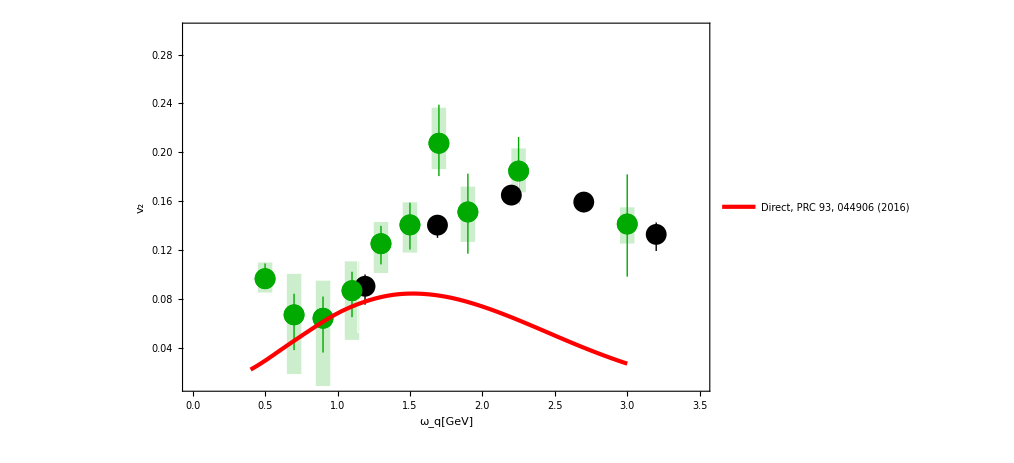

```mathematica
Show[Nv2b25eB13,v2P20401, v2P20402,v2P2040c1,v2P2040c2,Dat,v2Hydro]
```

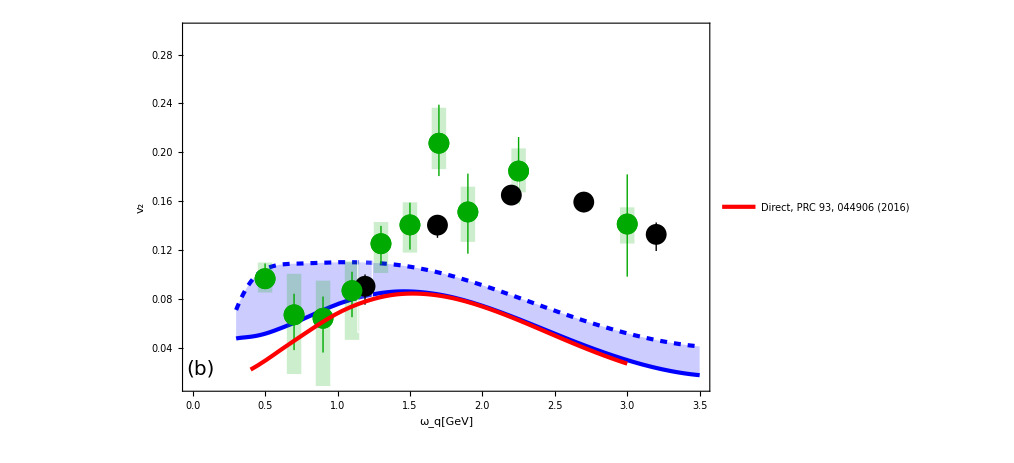

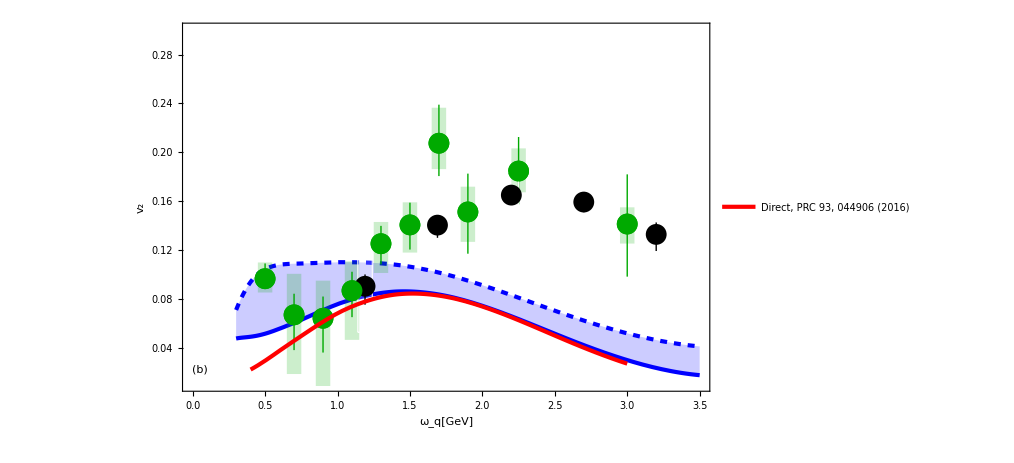

```mathematica
Show[Nv2LeB13,v2P20401, v2P20402,v2P2040c1,v2P2040c2,Dat,v2Hydro]
```

-Graphics-

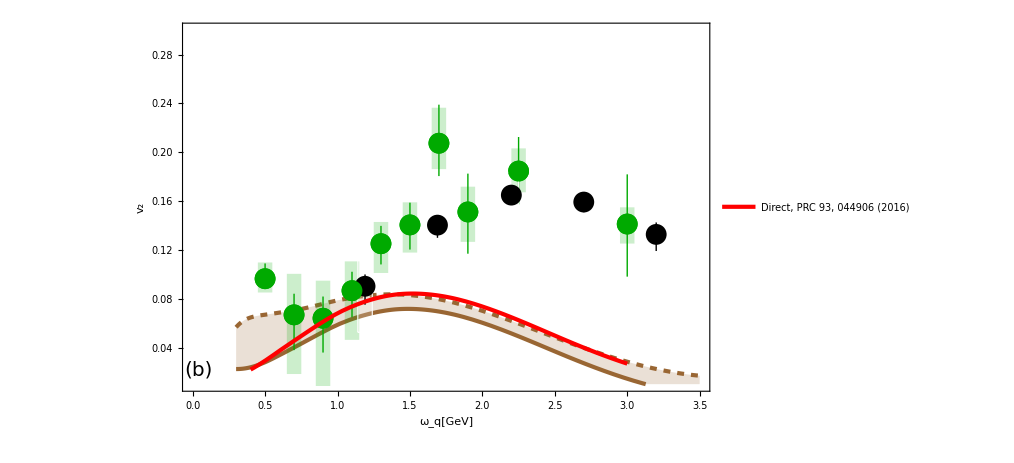

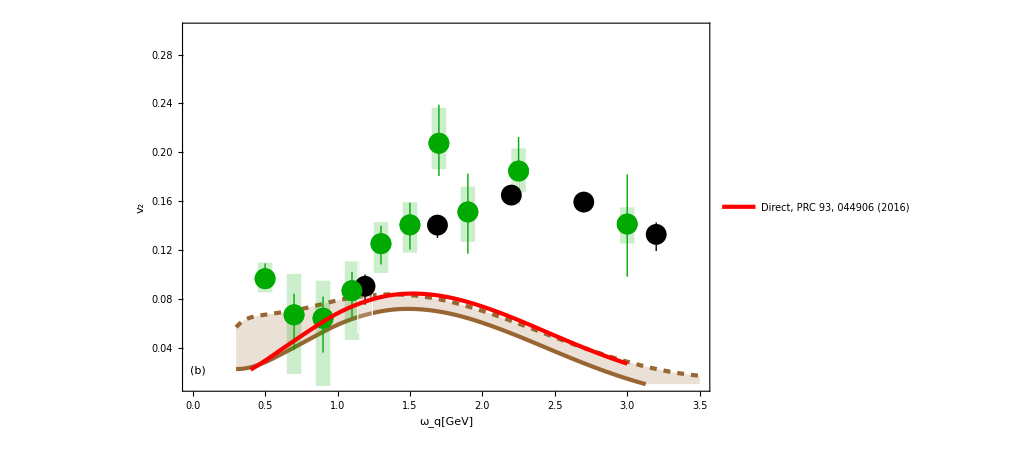

## yield Modelo, comparado con Datos-Hydro

```mathematica
Nyield13=
Quiet[LogPlot[{y1eB[ωq],y3eB[ωq]},{ωq,0.2,3.5},Filling->{1->{2}},PlotRange->{{0.1,3.5},{10^-4,20}},Frame->True,PlotStyle->{{Directive[Brown,AbsoluteThickness[3]]},{Directive[Brown,AbsoluteThickness[3],AbsoluteDashing[5]]}},ImageSize->{750,450},Frame->True,FrameStyle->Directive[Thick,Black,26],FrameTicks-> {{All,None},{All,None}},FrameLabel->{Style["ω_q[GeV]",26],Style["(1/2π ω_q)(dN/dω_q) [GeV^-2]",25]},PlotLegends->Placed[LineLegend[{Style["eB = m_π^2",26],Style["eB = 3m_π^2",26]},LegendMarkerSize->25],{Right,Center}]]];
```

```mathematica
Nyield13b25=
Quiet[LogPlot[{y1eB[ωq],y3eB[ωq]},{ωq,0.2,3.5},Filling->{1->{2}},PlotRange->{{0.1,3.5},{10^-4,20}},Frame->True,PlotStyle->{{Directive[Blue,AbsoluteThickness[3]]},{Directive[Blue,AbsoluteThickness[3],AbsoluteDashing[5]]}},ImageSize->{750,450},Frame->True,FrameStyle->Directive[Thick,Black,26],FrameTicks-> {{All,None},{All,None}},FrameLabel->{Style["ω_q[GeV]",26],Style["(1/2π ω_q)(dN/dω_q) [GeV^-2]",25]},PlotLegends->Placed[LineLegend[{Style["eB = m_π^2",26],Style["eB = 3m_π^2",26]},LegendMarkerSize->25],{Right,Center}]]];
```

```mathematica
yield515=
Quiet[LogPlot[{(dNdq[0.5eB,1,λ,μ,η,ωq,β]+2dNdq[0.5eB,2,λ,μ,η,ωq,β]),(dNdq[1.5eB,1,λ,μ,η,ωq,β]+2dNdq[1.eB,2,λ,μ,η,ωq,β])},{ωq,0.2,3},Filling->{1->{2}},PlotRange->{{0.1,3.05},{.0002,10}},Frame->True,PlotStyle->{{Directive[Blue,AbsoluteThickness[3]]},{Directive[Blue,AbsoluteThickness[3],AbsoluteDashing[5]]}},ImageSize->{750,450},Frame->True,FrameStyle->Directive[Thick,Black,26],FrameTicks-> {{All,None},{All,None}},FrameLabel->{Style["ω_q[GeV]",26],Style["(1/2π ω_q)(dN/dω_q) [GeV^-2]",25]},PlotLegends->Placed[{Style["eB = 0.5m_π^2",26],Style["eB = 1.5m_π^2",26]},{Right,Top}]]];
```

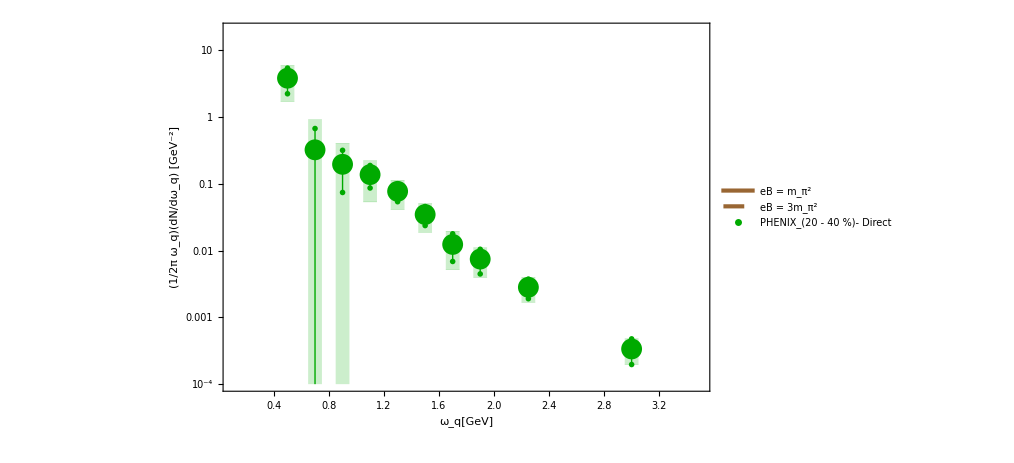

```mathematica
Show[Nyield13,DatSt,DatSy,DatDis]
```

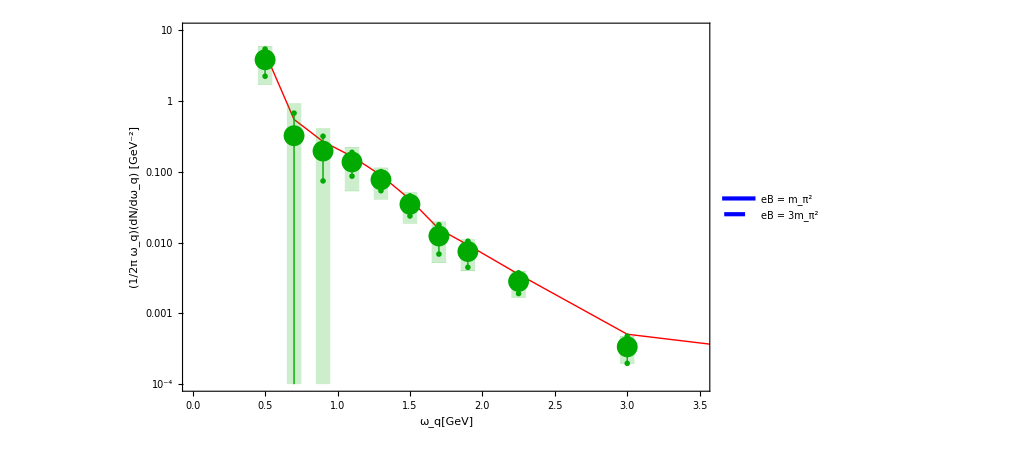

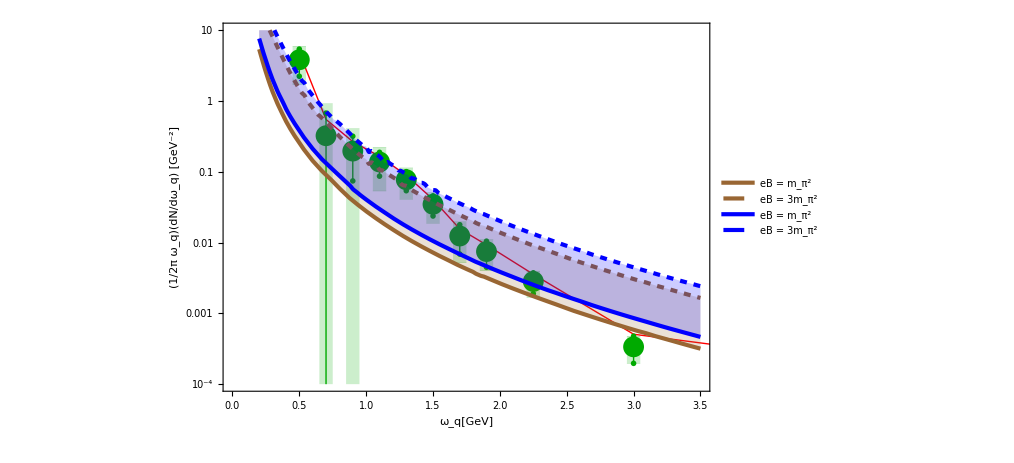

```mathematica
Show[DatDisnp,DatDis,DatSy,DatSt,Nyield13b25]
```

Show::gcomb: Could not combine the graphics objects in ….

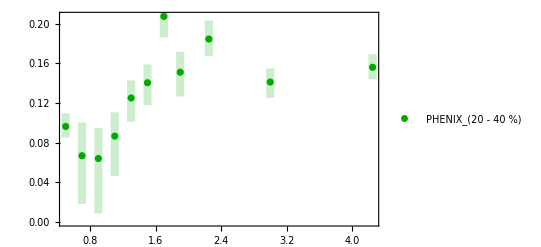
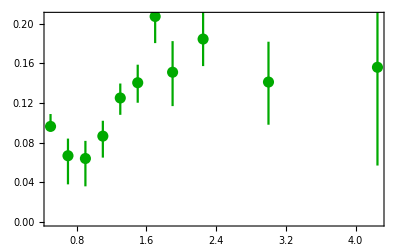
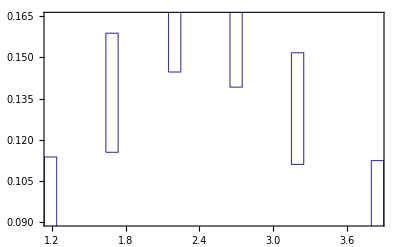
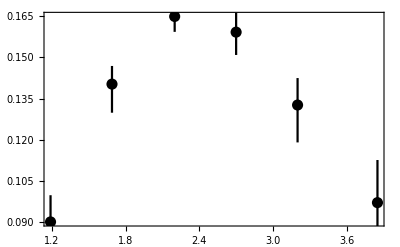
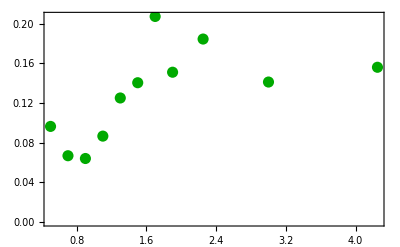
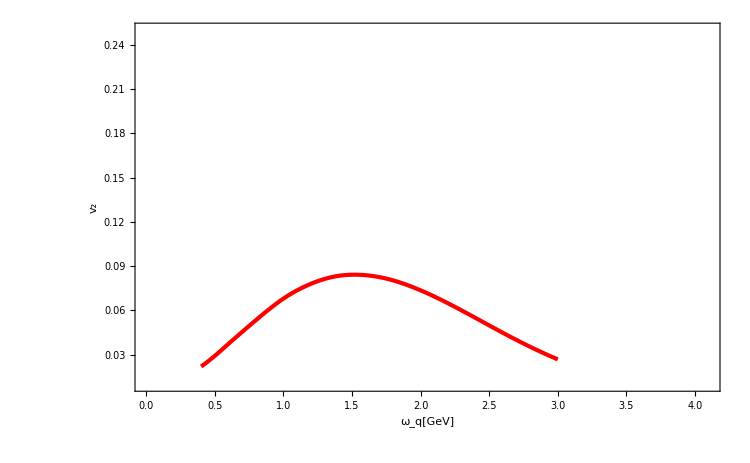
Show[v2LeB13,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
Show[v2LeB13,v2P20401, v2P20402,v2P2040c1,v2P2040c2,Dat,v2Hydro]
```